To reduce the time of overall calculation, this notebook describes how to bootstrap the following three-loop integrals. The bootstrap of four-loop integrals will be the same except that we need each step to be calculated to higher order.

```mathematica
Quit[];
```

```mathematica
dir=NotebookDirectory[];
dirasym=NotebookDirectory[]
```

/Users/windfolgen/Documents/Wolfram Mathematica/svbwalkthrough/

## Basic Functions

#### leading singularity

```mathematica
(*the position coordinates*)
Unprotect[x];
ClearAll[x];
x[a_,a_]:=0;
x/:x[a_]-x[b_]:=x[a,b];
x/:x[a_,b_]-x[c_,b_]:=x[a,c];
x/:x[a_,b_]-x[a_,c_]:=x[c,b];
x/:x[a_,b_]+x[b_,c_]:=x[a,c];
x/:x[a_,b_]+x[c_,a_]:=x[c,b];
x[a_,b_]/;(!OrderedQ[{a,b}]):=Signature[{a,b}]*x[Sequence@@(Sort[{a,b}])];
Protect[x];
```

```mathematica
Unprotect[V,VD,V2,SD];
ClearAll[V,VD,V2,SD];
SetAttributes[VD,Orderless];
V/:V[a_]*V[b_]:=VD[a,b];
V/:Power[V[a_],n_/;(EvenQ[n])]:=Power[V2[a],n/2];
V[Times[n_,x[a__]]]:=Times[n]*V[x[a]];
VD[0,a_]:=0;
VD[a_,a_]:=V2[a];
VD[a_,b_]/;(b=!=a):=If[MatchQ[Evaluate[(a-b)],x[__]|-x[__]],-1/2*(V2[a-b]-V2[a]-V2[b]),If[MatchQ[Evaluate[(a+b)],x[__]|-x[__]],1/2*(V2[a+b]-V2[a]-V2[b]),SD[a,b]]];
V2[0]:=0;
V2[-a_]:=V2[a];
Protect[V,VD,V2,SD];
```

```mathematica
ClearAll[ShowV2];
ShowV2[exp_]:=exp/.{HoldPattern[V2[x[a_,b_]]]:>Subscript[x, a,b]^2};
```

```mathematica
ClearAll[PerfectSquareOut];(*split the perfect square out of a square root*)
PerfectSquareOut[expr_]:=Module[{exp,list,sl={},nsl={}},
exp=expr//Factor;
If[exp===0,Return[{1,0}]];
If[Head[exp]===Power,If[MatchQ[exp,Power[_,_?EvenQ]],Return[{exp/.{Power[z_,n_]:>Power[z,n/2]},1}],Return[{exp/.{Power[z_,n_]:>Power[z,Quotient[n,2]]},exp/.{Power[z_,n_]:>z}}]]];
If[Head[exp]===Times,list=List@@exp,Return[{1,exp}]];
Do[
	If[MatchQ[list[[i]],Power[_,_]],
AppendTo[sl,list[[i]]/.{Power[z_,n_]:>Power[z,Quotient[n,2]]}];
AppendTo[nsl,list[[i]]/.{Power[z_,n_]:>Power[z,Mod[n,2]]}],
If[NumericQ[list[[i]]],AppendTo[sl,Sqrt[list[[i]]]],AppendTo[nsl,list[[i]]]]
],{i,1,Length[list]}];
Return[{Times@@sl,Times@@nsl}];(*sl is the perfect square after removing power, nsl is non-perfect square and it will remains in the square root*)
];
```

```mathematica
(*The Jacobian factor after cut for one loop momentum*)
ClearAll[Jacob];
Options[Jacob]={"outputlevel"->1};
Jacob[list_,v_,OptionsPattern[]]:=Module[{vlist,R,pow,rep,tem,jac,tag,y,sol,sim,result},
If[OptionValue["outputlevel"]>1,Print["        Calculating Jacobians for loop: ",Subscript[x,v]]];
If[Length[list]=!=4||Count[FreeQ[#,v]&/@list,False]=!=4,Print["four conditions needed for cut of the loop: ",x[v]];Return[$Failed]];
vlist=Cases[list,V2[a_/;(!FreeQ[{a},v])],Infinity]//DeleteDuplicates;
If[OptionValue["outputlevel"]>1,Print["        The four conditions are: ",list//ShowV2]];
rep=Thread@Rule[vlist,R*vlist];
pow=Exponent[#,R]&/@(list/.rep);
If[AnyTrue[pow,(#=!=1)&],Print["        the Jacbian need to be calculated by hand: ",list]];
rep=Thread@Rule[vlist,vlist/.{x->y}/.{V2[y[a_,v]]:>-2V[x[a,v]],V2[y[v,a_]]:>2V[x[v,a]]}];
(*Print["rep: ",rep];(*take the derivative*)*)
tem=list/.rep;
(*Print["tem: ",tem];*)
(*implement the cut condition*)
sol=Solve[Thread@Equal[list,0],vlist][[1]]//Quiet;
(*Print["sol: ",sol];*)
jac=Table[tem[[i]]*tem[[j]]//Expand,{i,1,Length[tem]},{j,1,Length[tem]}]/.sol//Expand;
sim=Det[jac-DiagonalMatrix[Diagonal[jac]]]//Factor;
If[OptionValue["outputlevel"]>1,Print["        The corresponding Jacobian matrix is: ",MatrixForm[jac//Factor//ShowV2]]];
tag=((Cases[#,HoldPattern[x[a_,v]|x[v,a_]]->a,Infinity]//DeleteDuplicates)&/@list)/.{{a_}:>a}//DeleteDuplicates;
result=PerfectSquareOut[Det[jac]//Factor];
If[FreeQ[result[[1]],V2],Return[{Subscript[λ,tag],{result[[1]],Plus@@{(sim/result[[1]]^2//Factor),-((sim-Det[jac])/result[[1]]^2//Factor)}}}],Return[{Subscript[λ,tag],result}]];
];
```

```mathematica
ClearAll[AdmissibleCutQ];
Options[AdmissibleCutQ]={deBug->False};
AdmissibleCutQ[cut_,var_,replambda_,OptionsPattern[]]:=Module[{temint,temhint,vlist,powint,powhint,rep,R},
temint=DeleteCases[cut,_?(!FreeQ[#,λ]&)];
temhint=Complement[cut,temint]/.replambda;
vlist=Cases[Join[temint,temhint],HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity]//DeleteDuplicates;
If[OptionValue[deBug],Print["temint: ",temint];Print["temhint: ",temhint];Print["vlist: ",vlist]];
If[Length[vlist]<4,Return[False]];(*there are less than 4 variables, then this cannot be a complete cut*)
rep=Thread@Rule[vlist,R*vlist];
powint=Exponent[#,R]&/@(temint/.rep);
powhint=Floor[(Exponent[#,R]/2)]&/@(temhint/.rep);
If[Total[powint]+Total[powhint]<4,Return[False]];(*the conditions are less than 4*)
Return[True];
];
```

```mathematica
ClearAll[ResolveCondition];(*this is used to deal with quadratic polynomials in the intermediate steps*)
Options[ResolveCondition]={"num"->1};
ResolveCondition[list_,var_,OptionsPattern[]]:=Module[{pow,vlist,nvlist,R,rep,pos,result,dis,a,tem,tag,replam,sys,sol,exp},
result=list;
vlist=Cases[list,HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity]//DeleteDuplicates;
nvlist=Cases[{OptionValue["num"]},HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity]//DeleteDuplicates;(*variables in the numerator*)
rep=Thread@Rule[vlist,R*vlist];
pow=Exponent[#,R]&/@(list/.rep);
If[Max[pow]<2,Return[{result,{},{},1}]];(*all linear polynomial, no need to resolve*)
If[Count[pow,2]==1,
(*only one quadratic polynomials present*)
pos=Position[pow,2][[1,1]];
(*this quadratic polynomial may need simplificatopn*)
sys=Thread@Equal[Delete[list,pos],0];
sol=Solve[sys,vlist][[1]]//Quiet;
exp=list[[pos]]/.sol//Factor;
vlist=Cases[{exp},HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity]//DeleteDuplicates;
If[Intersection[nvlist,vlist]==={},
Print[Style["        variabels do not exist in the numerator. solve either one: ",Magenta],vlist],
vlist=Intersection[nvlist,vlist];
Print[Style["        solve variable: ",Magenta],vlist];
];
result[[pos]]=D[exp,vlist[[1]]];(*replace it with the derivative, but we need to balance the power with its discriminant*)
a=Coefficient[exp,vlist[[1]],2];
dis=PerfectSquareOut[Discriminant[exp,vlist[[1]]]];
tem=List@@(Times@@Join[result,{dis[[1]]}])//DeleteCases[#,_?NumericQ]&;
tag={Cases[dis[[2]],HoldPattern[x[a_,b_]]->{a,b},Infinity]//Flatten//DeleteDuplicates,Hash[dis[[2]],"Expression"]};
replam=Rule[Subscript[λ,tag],dis[[2]]];
tem=Append[tem,Subscript[λ,tag]]//GatherBy[#,(FreeQ[#,HoldPattern[x[_,var]]|HoldPattern[x[var,_]]])&]&//SortBy[#,(FreeQ[#,HoldPattern[x[_,var]]|HoldPattern[x[var,_]]])&]&;
Return[{tem[[1]],Drop[tem,1]//Flatten,{replam},a}],
Print[Style["        2 or more quadratic polynomials!",Red," list: ",list];Return[{result,{},{},1}]]
]
];
```

```mathematica
ClearAll[ReOrganize];(*reorganize the square roots involved*)
ReOrganize[tem2_]:=Module[{rl,sl,nsl},
If[tem2==={},Return[{{},{}}]];
rl=tem2[[All,1]];
sl=tem2[[All,2]];
nsl=PerfectSquareOut[Times@@sl];
rl=Append[rl,nsl[[1]]];
nsl=If[Head[nsl[[2]]]===Times,List@@nsl[[2]],{nsl[[2]]}];
Return[{rl,nsl//DeleteCases[#,_?NumericQ]&}];
];
```

```mathematica
ClearAll[CutOneLoop];
Options[CutOneLoop]={deBug->True};
CutOneLoop[cutlist_,numlist_,var_,replambda_,remain_,OptionsPattern[]]:=Module[{select,subset,i,jacob,tem,temvar,tem1,tem2,tem22,tem3,temlist,den,num,sol,temsol,sys,const,j,k,l,s,tag,replam={},result,num1,den1,temsys,temsys1,temsys2,sqrt,mark,temmark,temnum,checksol={},checkps},
Print["    cut ",cutlist," for ",Subscript[x,var],". numerator: ",Style[Times@@numlist,RGBColor[0.4,0.53,1.]]];
select=Select[cutlist,Not@FreeQ[#,var]&];
subset=Select[Subsets[select,4],AdmissibleCutQ[#,var,replambda]&];(*we choose proper subset that can contribute 4 conditions, some lower sets can also contribute 4 conditions*)
Print["    totally ",Length[subset]," cases:"];
(*If[subset==={},Print["select: ",select];Print["replambda: ",replambda]];*)
result=Reap[
Do[
Print[Style["        case ",Orange,15],i,": ",subset[[i]]];
tem1=DeleteCases[subset[[i]],_?(!FreeQ[#,λ]&)];
tem2=(Cases[subset[[i]],_?(!FreeQ[#,λ]&)])/.replambda;(*terms related to square roots*)
tem3=(Cases[{#},HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity]//DeleteDuplicates)&/@Join[tem1,tem2];
temvar=Flatten[tem3]//DeleteDuplicates;(*the variables involving loop momenta*)
If[Length[temvar]<4,Print["        variable not enough. temvar: ",temvar];Continue[]];(*variables less than 4, not solvable*)

sys=tem1;(*initial cut system. cut terms which are not square roots*)
If[OptionValue[deBug],Print["temvar: ",temvar];Print["initial sys: ",sys]];
sol=Solve[Thread@Equal[sys,0],temvar][[1]]//Quiet;
k=1;
const={};(*keep track of constant terms*)
checksol={};(*this solution can be used to check some cancellation between numerator and denominator*)
While[Length[sol]<4&&k<5,(*when the solution is not enough, we substitute the initial solution into remaining square roots*)
If[Length[subset[[i]]]>=4&&tem2==={},
Print[Style["        the conditions may be not enough for ",Magenta],Subscript[x,var],". cut list: ",cutlist," sublist: ",subset[[i]]]
];(*this is for the case where expression under square roots are also used but the condition is still not enough*)

tem22=PerfectSquareOut/@(tem2/.sol);(*take care of cases where the square root is 0 under current solution*)
If[MemberQ[tem22,{1,0}],(*if the cut is 0, then we add the expression with less cut to the system*)
Print[Style["        square root is 0",Magenta]," need less cut for the polynomial under square root: ",Short[tem2,20]];
s=1;
While[MemberQ[tem22,{1,0}]&&s<Length[sol],
tem22=PerfectSquareOut/@(tem2/.Drop[sol,-s]);
checksol=Drop[sol,-s];(*this solution can be used to check some cancellation between numerator and denominator*)
s=s+1;
];
If[MemberQ[tem22,{1,0}],Print[Style["        something is wrong! this square root is 0 from the beginning: ",Red],Complement[subset[[i]],tem1]]];
tem2=tem22
,
tem2=tem22
];
tem2=ReOrganize[tem22];(*in case two square roots coincide with each other,tem2 is reorganized that tem[[1]] is the rational list and tem[[2]] is the square roots*)
checkps=Select[tem2[[1]],IntersectingQ[Cases[{#},HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity],temvar]&];(*check whether double pole exist*)
If[Not@FreeQ[Times@@checkps//Factor,Power[_,_?(#>1&)],{0,1}]&&checksol==={},
Print["        double pole find!"," checkps: ",checkps," sol: ",sol];
checksol=sol;];(*when there is a double pole, we record the solution before solve this double pole, since the numerator can cancel the pole after substituting the solution recorded*)
const=Join[const,Select[tem2[[1]],Not@IntersectingQ[Cases[{#},HoldPattern[V2[x[_,var]]]|HoldPattern[V2[x[var,_]]],Infinity],temvar]&]];
If[Complement[tem2[[1]],const]==={},tem2=tem2[[2]];Break[]];(*no new conditions*)
sys=Join[sys,checkps];
sol=Solve[Thread@Equal[sys,0],temvar]//Quiet;
If[sol==={},Print[Style["        no solution! check the system: ",Red],sys," temvar: ",temvar],
If[Length[sol]>1,
sol=(sol//SortBy[#,LeafCount]&)[[1]];
Print["        multiple solutions exist! pick up the simpler one: ",sol],
sol=sol[[1]]]];
tem2=tem2[[2]]//DeleteCases[#,_?NumericQ]&;
k=k+1;
];
If[Length[sol]<4&&tem2=!={},(*if the solution is still not enough after solving the square roots*)
Print[Style["        the condition is not enough for ",Red],Subscript[x,var],". sys : ",sys];
Print[Style["        original square root is: ",Cyan],Complement[subset[[i]],tem1]/.replambda/.sol//Factor];Print[Style["        the remaining square root is: ",Cyan],tem2];Print[Style["        you may need to consider cutting two loops in the same time or this is a elliptic cut!",Cyan]," cut list: ",cutlist];
Continue[]
];
replam=replambda;
sys=Join[sys,const];
If[OptionValue[deBug],Print["sys: ",sys]];
If[tem2=!={},
If[Not@FreeQ[tem2,HoldPattern[x[_,var]]]||Not@FreeQ[tem2,HoldPattern[x[var,_]]],
Print[Style["        this case need to be solved by hand!",Red]," sys: ",sys," square root: ",tem2];
Continue[]
];
Print[Style["        additional square roots present: ",RGBColor[0.52,0.54,1.]],Sqrt[ShowV2[tem2]]];
tag=({Cases[#,HoldPattern[x[a_,b_]]->{a,b},Infinity]//Flatten//DeleteDuplicates,Hash[#,"Expression"]})&/@tem2;
replam=Join[replam,Thread@Rule[Subscript[λ,#]&/@tag,tem2]];
sys=Join[sys,Subscript[λ,#]&/@tag];(*add square root parts back!*)
];
(*sometimes there are more conditions than 4 in the sys!(some may be cancelled by numerator). in this case, we should split them and re-calculate*)
num=Times@@numlist;
If[checksol=!={},
num=num/.checksol;
If[num===0&&((Times@@(Complement[select,subset[[i]]])/.checksol)=!=0),Print[Style["        this cut is 0. check it: ",Magenta],"sys: ",sys," select: ",select,"numerator: ",Times@@numlist],
If[num===0,num=Times@@numlist,Print["        numerator simplified from ",Times@@numlist," to ",num]]]
];(*in this case, the denominator is given after substituting checksol so the numerator should also substitute the value*)
den=Times@@Select[List@@Times@@sys,MatchQ[#,Power[_,_?(#>1&)]]&];(*higher pole must be cancelled by numerator*)
If[den=!=1,
Print["        higher power pole encountered, it should be cancelled by numerator: ",den];];
tem=num/(den)//Cancel;
num=Numerator[tem];
den=(Times@@sys)*Denominator[tem]/den;
If[Head[den]=!=Times,
Print[Style["        the numerator cancels most of the denominator. cut condition is not enough: ",Red],tem];
Continue[],
sys=List@@den;
];
temsys=sys//Flatten//DeleteCases[#,_?NumericQ]&//GatherBy[#,(FreeQ[#,HoldPattern[x[_,var]]|HoldPattern[x[var,_]]])&]&//SortBy[#,(FreeQ[#,HoldPattern[x[_,var]]|HoldPattern[x[var,_]]])&]&;
If[OptionValue[deBug],Print["temsys: ",temsys]];
If[Length[temsys[[1]]]<4,
(*replace the quadratic conditions with linear ones*)
tem=ResolveCondition[temsys[[1]],var,"num"->num];
temsys[[1]]=tem[[1]];
temsys1=Subsets[tem[[1]],{4}];(*cut equations*)
temsys2=Join[Drop[temsys,1]//Flatten,tem[[2]]];(*constant terms*)
replam=Join[replam,tem[[3]]];(*replacement rule*)
num=num*tem[[4]];(*numerator*)
Print[Style["        the cut condition has been resolved!",Magenta]," sys: ",tem],
temsys1=Subsets[temsys[[1]],{4}];
temsys2=Drop[temsys,1]//Flatten;
];
Print["        the condition of cuts can be further split into: ",ShowV2[temsys1]];
Print["        the constant term is ",Times@@temsys2];

temnum=num;
Do[
sys=temsys1[[l]];
sol=Solve[Thread@Equal[sys,0],temvar][[1]]//Quiet;(*pick up 4 and solve them*)
jacob=Jacob[sys,var,"outputlevel"->2];
replam=Join[replam,{Rule[jacob[[1]],jacob[[2,2]]]}];
(*substitute solutions into the remaining expressions after cut*)
den=Join[Complement[cutlist,subset[[i]]],{jacob[[1]],jacob[[2,1]]},temsys2(*constant term*),Complement[temsys[[1]],sys](*terms not cut*)];
num=temnum;
If[OptionValue[deBug],Print["den: ",den];Print["num: ",num]];
tem1=DeleteCases[den,_?(!FreeQ[#,λ]&)];
tem2=Cases[den,_?(!FreeQ[#,λ]&)];
tem1=Join[tem1,DeleteCases[tem2,_?(!FreeQ[#,var]&)]];(*terms not relevant to square root of current loop*)
sqrt=Cases[tem2,_?(!FreeQ[#,var]&)]/.replam;
tem2=PerfectSquareOut/@(sqrt/.sol);(*square roots relevant to the current loop momentum*)
If[MemberQ[tem2,{1,0}],(*some square roots can be 0 under the solution*)
mark=0;
Print[Style["        square root is 0",Magenta]," be careful of the expression under square root: ",sqrt],
mark=1;(*if it is not 0, the expression will be merged with the main part*)
If[Not@FreeQ[tem2[[All,2]],HoldPattern[x[_,var]]|HoldPattern[x[var,_]]],(*if some remaining expression for this loop momentum is not solved*)
Print[Style["        the loop momentum has not been totally solved: ",Red],Subscript[x,var]," sol: ",sol," remaining expression under square root: ",tem2];
Continue[];
];
tem1=Join[tem1,tem2[[All,1]]];
tem3=(tem2[[All,2]]//DeleteCases[#,_?NumericQ]&);
If[tem3=!={},(*there are remaining terms under square roots after substituting the solution*)
tag=({Cases[#,HoldPattern[x[a_,b_]]->{a,b},Infinity]//Flatten//DeleteDuplicates,Hash[#,"Expression"]})&/@tem3;
replam=Join[replam,Thread@Rule[Subscript[λ,#]&/@tag,tem3]];
tem1=Join[tem1,Subscript[λ,#]&/@tag];
];
];
den=Times@@tem1;
tem={num,den*mark}/.sol//Factor;
If[tem==={0,0},
Print[Style["        indeterminant encountered! the solving order is important: ",Pink]];
tem1=Subsets[sys,{3}];(*here we assume one cut less can save the 0/0 danger*)
Do[
temsol=Solve[Thread@Equal[tem1[[j]],0],temvar][[1]]//Quiet;
If[mark===0,(*when the square root is 0*)
tem2=PerfectSquareOut/@(sqrt/.temsol);
If[MemberQ[tem2,{1,0}],
temmark=0,
temmark=Times@@(tem2[[All,1]]);
tem3=(tem2[[All,2]]//DeleteCases[#,_?NumericQ]&);
If[tem3=!={},(*there are remaining terms under square roots after substituting the solution*)
tag=({Cases[#,HoldPattern[x[a_,b_]]->{a,b},Infinity]//Flatten//DeleteDuplicates,Hash[#,"Expression"]})&/@tem3;
replam=Join[replam,Thread@Rule[Subscript[λ,#]&/@tag,tem3]];
temmark=temmark*(Times@@(Subscript[λ,#]&/@tag))
];
],
temmark=1;
];
tem=({num,den*temmark}/.temsol//Factor);
If[tem==={0,0}||MatchQ[tem,{_,0}],
Continue[],
Print[Style["            one solving order identified: ",Pink],temsol];
tem=tem[[1]]/tem[[2]]//Factor;
If[tem===0||(((Numerator[tem]/.sol)===0)&&((Denominator[tem]/.sol)=!=0)),Print["        this cut is 0."];Continue[]];(*this cut is 0*)
If[Not@FreeQ[tem,HoldPattern[x[_,var]]|HoldPattern[x[var,_]]],(*if some remaining expression for this loop momentum is not solved*)
Print[Style["        the loop momentum has not been totally solved: ",Red],Subscript[x,var]," sol: ",sol," remaining {den,num}: ",{den*temmark,num}," num/den: ",tem];
Continue[];
];
num1=Numerator[tem];
den1=Denominator[tem];
If[Head[num1]===Times,num1=List@@num1,num1={num1}];
If[Head[den1]===Times,den1=List@@den1,den1={den1}];
Print[Style["        the remaining expression is ",Blue],TableForm[{Times@@den1,Times@@num1}]];
Sow[{den1//DeleteCases[#,_?NumericQ]&,num1//DeleteCases[#,_?NumericQ]&,replam,Complement[remain,{var}]}]
];
,{j,1,Length[tem1]}];
Continue[];
];
tem=tem[[1]]/tem[[2]]//Factor;
If[Not@FreeQ[tem,HoldPattern[x[_,var]]|HoldPattern[x[var,_]]],(*if some remaining expression for this loop momentum is not solved*)
Print[Style["        the loop momentum has not been totally solved: ",Red],Subscript[x,var]," sol: ",sol," remaining {den,num}: ",{den,num}," num/den: ",tem];
Continue[];
];
If[tem===0,Print["        this cut is 0."];Continue[]];(*this cut is 0*)
num1=Numerator[tem];
den1=Denominator[tem];
If[Head[num1]===Times,num1=List@@num1,num1={num1}];
If[Head[den1]===Times,den1=List@@den1,den1={den1}];
Print[Style["        the remaining expression is ",Blue],TableForm[{Times@@den1,Times@@num1}]];
Sow[{den1//DeleteCases[#,_?NumericQ]&,num1//DeleteCases[#,_?NumericQ]&,replam,Complement[remain,{var}]}]
,{l,1,Length[temsys1]}];

,{i,1,Length[subset]}];
][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
```

```mathematica
ClearAll[ResolveOrder];(*resolve the solving order of loop momenta*)
Options[ResolveOrder]={"order"->0};
ResolveOrder[den_,num_,loops_,OptionsPattern[]]:=Module[{var,numlabel,denlabel,slist,order},
numlabel=Cases[{#},HoldPattern[x[a_,b_]]->{a,b},Infinity]&/@num//Flatten[#,1]&;
denlabel=Cases[den,Subscript[λ,a_]:>(a//Flatten),Infinity];
(*Print["numlabel: ",numlabel];
Print["numlabel: ",denlabel];*)
slist=Reap[
Do[
If[AnyTrue[denlabel,ContainsAll[#,numlabel[[j]]]&],Sow[numlabel[[j]]]]
,{j,1,Length[numlabel]}]
][[2]];
If[slist==={},Print["       There may be no solvable order of variables:","den: ",den,"num: ",num],slist=slist[[1]]];
order=Table[{Count[FreeQ[#,loops[[i]]]&/@num,False],-Count[FreeQ[#,loops[[i]]]&/@slist,False],-Count[FreeQ[#,loops[[i]]]&/@denlabel,False],loops[[i]]},{i,1,Length[loops]}]//SortBy[#,{First,#[[2]]&,#[[3]]&}]&;
If[OptionValue["order"]==0,Return[order[[All,-1]]],Return[order[[All,-1]]//Reverse]];
];
```

```mathematica
ClearAll[LeadingSingularities];
Options[LeadingSingularities]={deBug->False,"outputlevel"->2,"external"->{1,2,3,4},"order"->0};
LeadingSingularities[integrand_,OptionsPattern[]]:=Module[{graph,agraph,sgraph,edgeden,edgenum,loops,tem,pos,tem1,tem2,remain,k=1,l,cutlist,numlist,temcut,temnum,jacob,replambda={},subset,temrep,ls},
If[Head[Denominator[integrand]]===Plus||Head[Numerator[integrand]]===Plus,Print["The denominator or numerator should be monomial!"];Return[$Failed]];
edgeden=UndirectedEdge@@@(Cases[Denominator[integrand],HoldPattern[x[_,_]],Infinity]);
edgenum=UndirectedEdge@@@(Cases[Numerator[integrand],HoldPattern[x[_,_]],Infinity]);
graph=Graph[Join[edgeden,edgenum],VertexLabels->"Name",VertexStyle->Thread@Rule[OptionValue["external"],Red],EdgeStyle->Thread@Rule[edgenum,Dashed]];
(*Print["the graph: ",graph];*)
Print["denom graph: ",Graph[edgeden,VertexLabels->"Name",VertexStyle->Thread@Rule[OptionValue["external"],Red]]];
loops=Complement[VertexList[graph],OptionValue["external"]];
Print["the loop variables are ",Subscript[x,#]&/@loops];
cutlist=(V2/@edgeden)/.{UndirectedEdge->x};(*the candidated to be cut is set to denominators at first*)
numlist=If[Head[Numerator[integrand]]===Times,List@@Numerator[integrand],{Numerator[integrand]}]/.{HoldPattern[x[a_,b_]]:>V2[x[a,b]]};(*the numerator list records the numerators which may be useful in the multivariate cut*)
(*given an integrand, we first choose some one which can be integrated out directly*)
tem=VertexDegree[graph,#]&/@loops;
If[Min[tem]<4,
Print["the input is wrong! degree of ",Subscript[x,#]&/@(Position[tem,Min[tem],1]//Flatten)," is not enough!"];Return[$Failed],
pos=Position[tem,4,1]//Flatten;
If[pos==={},Print["no loop variable can be integrated out first!"];Return[$Failed]];
tem1=loops[[pos]];(*possible loop variables that can be directly integrated out*)
(*If[OptionValue[deBug],Print["tem1: ",tem1]];*)
If[Length[pos]==1,
Print[Style["Step",18]," 1: integrate ",Subscript[x,tem1[[1]]]," first."],
agraph=VertexDelete[graph,OptionValue["external"]];(*graph with external points deleted*)
(*check the connectivity among the remaining loop variables*)
tem2={Length[Intersection[VertexComponent[agraph,{#},1],tem1]],#}&/@tem1//SortBy[#,First]&;
(*then we select loop variables in above list to integrate it out*)
remain=tem2[[All,2]];
k=1;
(*If[OptionValue[deBug],Print["remain: ",remain]];*)
tem1=Reap[
While[remain=!={}&&k<5,
Sow[remain[[1]]];
remain=Complement[remain,VertexComponent[agraph,{remain[[1]]},1]];
k=k+1;
]
][[2,1]];
Print[Style["Step",18]," 1: integrate ",Subscript[x,#]&/@tem1," first."]
];
];
(*next we integrate the loops selected out*)
Do[
tem=Select[cutlist,!FreeQ[#,tem1[[i]]]&];
If[Length[tem]=!=4,Print["    something is wrong! the condition for ",Subscript[x,tem1[[i]]]," is not 4"]];
cutlist=Complement[cutlist,tem];
jacob=Jacob[tem,tem1[[i]],"outputlevel"->2];
AppendTo[replambda,Rule[jacob[[1]],jacob[[2,2]]]];(*replacement rule for abbreviation*)
cutlist=(FactorList[#][[All,1]]&/@Join[cutlist,{jacob[[1]],jacob[[2,1]]}])//Flatten//DeleteCases[#,_?NumericQ]&;
,{i,1,Length[tem1]}];
If[OptionValue["outputlevel"]==1,Return[{cutlist,numlist,replambda}]];

(*now we continue to integrate out loop variables one by one*)
loops=Complement[loops,tem1];
remain=loops;
cutlist={{cutlist,numlist,replambda,remain}};
k=2;
While[remain=!={}&&k<8,
Print["    remaining loops: ",remain," length of remaining term: ",Length[cutlist]];
Print[Style["Step ",18],k," : cut the ",Switch[k,2,"2nd",3,"3rd",_,ToString[k]<>"-th"]," loop variable. "];
tem2=Reap[
Do[
temcut=cutlist[[l,1]];
temnum=cutlist[[l,2]];
remain=cutlist[[l,4]];
tem=Table[{Count[FreeQ[#,remain[[i]]]&/@temcut,False],remain[[i]]},{i,1,Length[remain]}]//SortBy[#,First]&;(*count the number for every remaining loop*)
Print[Style["the ",Orange,15],Switch[l,1,"1st",2,"2nd",3,"3rd",_,ToString[l]<>"-th"]," cut:"];
If[Max[tem[[All,1]]]<4,Print[Style["    the cut condition may be not enough!",Magenta]," cutlist: ",cutlist[[l]]];];
pos=FirstPosition[tem[[All,1]],4];
If[pos===Missing["NotFound"],
tem=ResolveOrder[temcut,temnum,remain,"order"->OptionValue["order"]];(*in this case, we order the loop momentum so that it can be solved in the next step*)
tem1=CutOneLoop[temcut,temnum,tem[[1]],cutlist[[l,3]],remain,deBug->OptionValue[deBug]];
If[tem1==={},Print[Style["    no cut detected for loop ",Red],Subscript[x,tem[[1]]]]];
Sow[tem1];
remain=Complement[remain,{tem[[1]]}],
tem1=CutOneLoop[temcut,temnum,tem[[pos[[1]],2]],cutlist[[l,3]],remain,deBug->OptionValue[deBug]];
If[tem1==={},Print[Style["    no cut detected for loop ",Red],Subscript[x,tem[[pos[[1]],2]]]]];
Sow[tem1];
remain=Complement[remain,{tem[[pos[[1]],2]]}]
];
,{l,1,Length[cutlist]}]
][[2]];
If[tem2=!={},tem2=Flatten[tem2[[1]],1]];
cutlist=tem2;
Print["    number of cut got: ",Length[cutlist]];
k=k+1;
];
If[Length[OptionValue["external"]]>4,Return[cutlist]];
Print[Style["Last Step: ",18]," expressing the leading singularities with u and v. ","u=",ShowV2[(V2[x[1,2]]*V2[x[3,4]])/(V2[x[1,3]]*V2[x[2,4]])],"v=",ShowV2[(V2[x[1,4]]*V2[x[2,3]])/(V2[x[1,3]]*V2[x[2,4]])]];
ls=Reap[
Do[
temnum=(Times@@cutlist[[i,2]])/.{V2[x[1,2]]->u*V2[x[1,3]]*V2[x[2,4]]/V2[x[3,4]],V2[x[1,4]]->v*V2[x[1,3]]*V2[x[2,4]]/V2[x[2,3]]};
temrep=Thread@Rule[Keys[cutlist[[i,3]]],(#[[1]]*Sqrt[#[[2]]])&/@(PerfectSquareOut/@(Values[cutlist[[i,3]]]/.{V2[x[1,2]]->u*V2[x[1,3]]*V2[x[2,4]]/V2[x[3,4]],V2[x[1,4]]->v*V2[x[1,3]]*V2[x[2,4]]/V2[x[2,3]]}))];(* replacement for λs *)
temcut=(Times@@cutlist[[i,1]]/.temrep)/.{V2[x[1,2]]->u*V2[x[1,3]]*V2[x[2,4]]/V2[x[3,4]],V2[x[1,4]]->v*V2[x[1,3]]*V2[x[2,4]]/V2[x[2,3]]};
Sow[temnum/temcut//Factor]
,{i,1,Length[cutlist]}]
][[2]];
If[ls=!={},
If[OptionValue["outputlevel"]!=2,Return[{ls[[1]],cutlist[[All,3]]}],Return[ls[[1]]]];,
Return[{}]];
];
```

#### canonical binary DCI integrals

To construct a canonical DCI integrand for a given word

```mathematica
ClearAll[CanonicalDCI];
CanonicalDCI[word_]:=Module[{list,initial,int,count},
If[StringQ[word],list=ToExpression/@(StringPartition[word,1]),If[Head[word]===List,list=word]];
int=1/(x[1,5]x[2,5]x[3,5]x[4,5]);
count=6;
Do[
If[list[[i]]===0,
int=(int/.{x[a__]:>(x[a]/.{1->count})})*x[2,4]/(x[count,2]x[count,4])/x[1,count],
int=int*x[1,2]/(x[2,4]);
int=(int/.{4->count})/(x[4,count]*x[1,count]);
];
count=count+1;
,{i,2,Length[list]}];
Return[int];
];
ClearAll[drawGraph];
Options[drawGraph]={"withoutnum"->True,"planar"->False,"output"->False,"id"->False};
drawGraph[{int_,list_},OptionsPattern[]]:=Module[{g,num,numedge,tlist},
If[OptionValue["output"],Print["numerator: ",Numerator[int]," ordering: ",list]];
tlist=If[Head[list[[1]]]===List,list[[1]],list];
num=Numerator[int];
If[Head[num]===Times,num=List@@num,num={num}];
numedge=(num/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten)/.{x->UndirectedEdge}//DeleteCases[#,_?NumericQ]&;
If[OptionValue["id"],Return[Graph[Join[(List@@Denominator[int])/.{x->UndirectedEdge},(numedge//DeleteDuplicates)/.{UndirectedEdge[a_,b_]:>{UndirectedEdge[a,"a"<>ToString[a]<>ToString[b]],UndirectedEdge["a"<>ToString[a]<>ToString[b],b]}}//Flatten,Thread@UndirectedEdge[tlist,"a"]]]//CanonicalGraph]];
g=Graph[(List@@Denominator[int])/.{x->UndirectedEdge},VertexLabels->"Name"];
If[OptionValue["planar"]&&PlanarGraphQ[g],g=Graph[(List@@Denominator[int])/.{x->UndirectedEdge},VertexLabels->"Name",GraphLayout->"SpringEmbedding"]];
Graph[Join[EdgeList[g],numedge],AbsoluteOptions[g,VertexCoordinates][[1]],EdgeStyle->Thread@Rule[numedge,Dashed],VertexLabels->"Name",VertexStyle->Thread@Rule[tlist,Pink]]
];
drawGraph[int_,OptionsPattern[]]:=Module[{g,num,numedge},
Print["numerator: ",Numerator[int]];
num=Numerator[int];
If[Head[num]===Times,num=List@@num,num={num}];
numedge=(num/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten)/.{x->UndirectedEdge};
g=Graph[(List@@Denominator[int])/.{x->UndirectedEdge},VertexLabels->"Name"];
If[OptionValue["withoutnum"],PlanarGraph[g],Graph[Join[EdgeList[g],numedge],AbsoluteOptions[g,VertexCoordinates][[1]],EdgeStyle->Thread@Rule[numedge,Dashed],VertexLabels->"Name"]]
];
ClearAll[boxing];
boxing[int_,olist_]:=Module[{list,num,den,ll,nl,nnl,pos,npos,nint,nint1,g,fac,result},
If[Head[olist[[1]]]===List,list=olist[[1]],list=olist];
Print["the ordering of external legs is ",list, " the expression of svmpl is related to this ordering!"];
num=Numerator[int];
den=Denominator[int];
ll=(List@@(den*num))/.{Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten;
(*Print[ll];*)
nl=Table[Select[ll,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
pos=Position[nl,_?(Length[#]===1&),1]//Flatten;
If[pos==={},Print["none of the vertex can be shrink by boxing!"];Return[Null]];
(*Print[pos];
Print[nl[[pos[[1]],1]]];*)
result=Reap[Do[
Print[Style["acting on vertex ",Bold],list[[pos[[i]]]]];
nint=(nl[[pos[[i]],1]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]]]/x[list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*int)/.{x[a__]:>(x[a]/.Thread@Rule[List@@(nl[[pos[[i]],1]]),list[[pos[[i]]]]])}//Factor;
g=(List@@Denominator[nint]);
If[Not@FreeQ[g,Power[_,2]],
Print["double pole present!"];Continue[],
nnl=Table[Select[g,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
npos=Position[nnl,_?(Length[#]===1&),1]//Flatten
];
If[npos=!={},
Print["no renormalization factor! which means adding 0 to the generalized ladder in {z/(z-1),zb/(zb-1)} notation"];
Sow[{nint,{list}}],
fac=x[list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]]]/(x[list[[pos[[i]]]],list[[If[pos[[i]]+1-Length[list]>0,pos[[i]]+1-Length[list],pos[[i]]+1]]]]*x[list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]],list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]]]);
nint1=nint*fac//Factor;
g=(List@@Denominator[nint1]);
If[Not@FreeQ[g,Power[_,2]],
Print[g," can not renormalize with ",1/fac];npos={},
nnl=Table[Select[g,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
npos=Position[nnl,_?(Length[#]===1&),1]//Flatten
];
If[npos=!={},
Print["renormalization with factor: ", 1/fac," which means adding 1 to the generalized ladder in {z/(z-1),zb/(zb-1)} notation"];Sow[{nint1,{list}}],
fac=x[list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]],list[[If[pos[[i]]+1-Length[list]>0,1,pos[[i]]+1]]]]*x[list[[pos[[i]]]],list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]]]/(x[list[[pos[[i]]]],list[[If[pos[[i]]-1==0,-1,pos[[i]]-1]]]]*x[list[[If[pos[[i]]+2-Length[list]>0,pos[[i]]+2-Length[list],pos[[i]]+2]]],list[[If[pos[[i]]+1-Length[list]>0,pos[[i]]+1-Length[list],pos[[i]]+1]]]]);
nint1=nint*fac//Factor;
g=(List@@Denominator[nint1]);
If[Not@FreeQ[g,Power[_,2]],
Print[g, "can not renormalize with ",1/fac];npos={},
nnl=Table[Select[g,Not@FreeQ[#,list[[i]]]&],{i,1,Length[list]}];
npos=Position[nnl,_?(Length[#]===1&),1]//Flatten
];
If[npos=!={},Print["renormalization with factor: ", 1/fac," which means adding 1 to the generalized ladder in {1/(1-z),1/(1-zb)} notation" ];Sow[{nint1,{list}}],Print["can not act boxing again!"];Sow[{nint,{list}}]]
];
]
,{i,1,Length[pos]}]
][[2,1]];
Return[result];
];
boxing[{int_,olist_}]:=boxing[int,olist];
Clear[ToMaple];
ToMaple[exp_]:=(Join@@({#[[1]]/.{Power[x[a_,b_],c_]:>F[{a,b},-c]}/.{x[a_,b_]:>F[{a,b},-1]},#[[2]]/.{x[a_,b_]:>F[{a,b},1]}}&[(If[Head[#]===Times,List@@#,{#}]&/@NumeratorDenominator[#])&[exp]]))//DeleteCases[#,_?(Not@FreeQ[#[[1]],1]&)]&//InputForm//ToString//StringDelete[#,"F"]&;
```

Transform expressions to maple form for the input of package HyperlogProcedures.

#### drawGraphClaude

```mathematica
(*this function is written by Claude Sonnet 4.6 as a backup*)
```

```mathematica
Options[drawGraphClaude]={"withoutnum"->True,"planar"->False,"output"->False,"id"->False};
drawGraphClaude[{int_,list_},OptionsPattern[]]:=Module[{g,num,numedge,tlist,coordsAssoc,allVerts,passesThrough,needsCurveSet,edgeCounts,numedgeTagged,edgeShapeRules},(*Optionally print numerator and ordering*)If[OptionValue["output"],Print["numerator: ",Numerator[int]," ordering: ",list]];
(*Flatten list structure for external legs*)tlist=If[Head[list[[1]]]===List,list[[1]],list];
(*Parse numerator into a flat list of edges,expanding powers to multi-edges*)num=Numerator[int];
If[Head[num]===Times,num=List@@num,num={num}];
numedge=(num/. {Power[x[a__],n_]:>Table[x[a],{i,1,n}]}//Flatten)/. {x->UndirectedEdge}//DeleteCases[#,_?NumericQ]&;
(*Early return:canonical graph with auxiliary vertices for numerator edges*)If[OptionValue["id"],Return[Graph[Join[(List@@Denominator[int])/. {x->UndirectedEdge},(numedge//DeleteDuplicates)/. {UndirectedEdge[a_,b_]:>{UndirectedEdge[a,"a"<>ToString[a]<>ToString[b]],UndirectedEdge["a"<>ToString[a]<>ToString[b],b]}}//Flatten,Thread@UndirectedEdge[tlist,"a"]]]//CanonicalGraph]];
(*Build base graph from denominator edges*)g=Graph[(List@@Denominator[int])/. {x->UndirectedEdge},VertexLabels->"Name"];
(*Use SpringEmbedding for planar graphs if requested*)If[OptionValue["planar"]&&PlanarGraphQ[g],g=Graph[(List@@Denominator[int])/. {x->UndirectedEdge},VertexLabels->"Name",GraphLayout->"SpringEmbedding"]];
(*Associate each vertex with its layout coordinate*)coordsAssoc=AssociationThread[VertexList[g],AbsoluteOptions[g,VertexCoordinates][[1,2]]];
allVerts=VertexList[g];
(*True if point pc lies strictly between pa and pb along the segment.Uses the 2D cross product to measure perpendicular distance:we flag collinearity when perp-distance<5% of the edge length.*)passesThrough=Function[{pa,pb,pc},Module[{ab,ap,cross,dot,len2},ab=pb-pa;
ap=pc-pa;
cross=ab[[1]]*ap[[2]]-ab[[2]]*ap[[1]];
dot=ab.ap;
len2=ab.ab;
len2>1.*^-10&&Abs[cross]<0.05*len2&&0<dot<len2]];
(*Determine which unique edge types would visually overlap a denominator chain (i.e.some intermediate vertex lies on the straight edge segment)*)needsCurveSet=Select[DeleteDuplicates[numedge],Function[e,Module[{a,b,pa,pb,others},{a,b}=List@@e;
pa=coordsAssoc[a];
pb=coordsAssoc[b];
others=Complement[allVerts,{a,b}];
AnyTrue[others,passesThrough[pa,pb,coordsAssoc[#]]&]]]];
(*Count occurrences of each edge type so we know the multiplicity*)edgeCounts=Counts[numedge];
(*Tag each numerator edge instance with a unique ID "n1","n2",... so that multi-edges can be addressed and styled independently.UndirectedEdge[a,b,tag] is Mathematica's tagged-edge syntax.*)numedgeTagged=Block[{ctr=<||>},Map[Function[e,ctr[e]=Lookup[ctr,e,0]+1;
UndirectedEdge[e[[1]],e[[2]],"n"<>ToString[ctr[e]]]],numedge]];
(*Assign each tagged edge an EdgeShapeFunction with a curvature offset.Multi-edge offsets are ALWAYS spread symmetrically around 0:off_k=(k-(n+1)/2)*step,step=0.3 so for n=2 the offsets are-0.15 and+0.15 (opposite sides),for n=3 they are-0.3,0,+0.3,etc.This is independent of collinearity.The only collinearity adjustment:when a collinear edge's spread lands exactly at 0 (middle instance of an odd-sized group),we nudge it to step/2 so it doesn't overlap the denominator chain underneath.offset=0 for a lone,non-collinear edge->Automatic (straight line).*)edgeShapeRules=MapThread[Function[{orig,tagged},Module[{n,k,off},n=edgeCounts[orig];
k=ToExpression[StringDrop[tagged[[3]],1]];
off=(k-(n+1)/2)*0.3;
(*Collinear single edge,or middle of odd group:nudge away*)If[MemberQ[needsCurveSet,orig]&&off==0,off=0.15];
If[off==0.0,tagged->Automatic,With[{o=off},tagged->Function[{pts,e},{Dashed,BezierCurve[{pts[[1]],pts[[1]]+0.5*(pts[[-1]]-pts[[1]])+o*{-(pts[[-1]]-pts[[1]])[[2]],(pts[[-1]]-pts[[1]])[[1]]},pts[[-1]]}]}]]]]],{numedge,numedgeTagged}];
(*Final graph:denominator solid edges+numerator dashed edges.Tagged edges are individually addressable,so multi-edges and collinear overlaps are all rendered at distinct visual offsets.*)Graph[Join[EdgeList[g],numedgeTagged],AbsoluteOptions[g,VertexCoordinates][[1]],EdgeStyle->Thread@Rule[numedgeTagged,Dashed],EdgeShapeFunction->edgeShapeRules,VertexLabels->"Name",VertexStyle->Thread@Rule[tlist,Pink]]
];
```

#### GraphReduce

```mathematica
ClearAll[ModSym];(*mod out term that are related to each other by permutation of external vertices*)
Options[ModSym]={"points"->{1,2,3,4}};
ModSym[intlist_,OptionsPattern[]]:=Module[{permE,permI,iv,select={},flag=0,xlist},
xlist=Cases[intlist,x[a__]->{a},Infinity]//Flatten//DeleteDuplicates;
iv=Complement[xlist,OptionValue["points"]];
permE=Thread@Rule[OptionValue["points"],#]&/@Permutations[OptionValue["points"]];
permI=Thread@Rule[iv,#]&/@Permutations[iv];
select=Append[select,intlist[[1]]//Factor];
Do[
flag=1;
Do[
Do[
If[MemberQ[select,(intlist[[i]]/.{x[a__]:>(x[a]/.permI[[k]]/.permE[[j]])})//Factor],flag=0;Break[]];
,{k,1,Length[permI]}];
If[flag==0,Break[]]
,{j,1,Length[permE]}];
If[flag==1,AppendTo[select,intlist[[i]]//Factor]]
,{i,2,Length[intlist]}];
Return[select];
];
```

```mathematica
ClearAll[GraphReduce];
Options[GraphReduce]={"external"->{1,2,3,4}};
GraphReduce[int_,OptionsPattern[]]:=Module[{num,graph,list,result,temp},
num=Numerator[int]//Cases[#,x[__],Infinity]&//DeleteDuplicates;
graph=drawGraph[{int,OptionValue["external"]},"withoutnum"->False];
list=FindSubgraphIsomorphism[Graph[{1<->2,2<->3,2<->4,2<->5,4<->5}],graph,All];
result=Reap[
Do[
If[Not@MemberQ[num,x[list[[i]][4],list[[i]][5]]],Continue[]];(*if this is not a numerator, then pass*)
If[VertexDegree[graph,list[[i]][2]]=!=4||MemberQ[OptionValue["external"],list[[i]][3]],Continue[]];(*the degree of central vertex must be 4*)(*the vertex 3 must be internal*)
Sow[list[[i]]]
,{i,1,Length[list]}]
][[2]];
If[result==={},Return[{}],result=result[[1]]];
list=result//DeleteDuplicatesBy[#,(#/@{1,2,3})&]&;
Print[Length[list]," case(s) found after modding the symmetry"];
(*Print["Reducing the graph ... "];*)
result=Reap[
Do[
temp=list[[i]];
Sow[int*x[temp[1],temp[2]]*x[temp[2],temp[3]]*x[temp[2],temp[4]]*x[temp[2],temp[5]]/x[temp[4],temp[5]]/x[temp[1],temp[3]]//Factor]
,{i,1,Length[list]}]
][[2,1]];
Return[result];
];
```

#### Series expansions

```mathematica
ClearAll[SeriesExpansionInf];
Options[SeriesExpansionInf]={"additional"->1,"Yorder"->5};
SeriesExpansionInf[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{zz->1/u/z}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz*u,-a]})/(-√(-4 u+(-1-u+v)^2)))/.zrep/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],P[0]->-Log[u]}/.{z->(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u),zz->(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansionInfP];
Options[SeriesExpansionInfP]={"additional"->1,"Yorder"->5};
SeriesExpansionInfP[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{zz->v/u/z}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz*u/v,-a]})/(-√(-4 u v+(-1+u+v)^2)))/.zrep/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],P[0]->-Log[u/v]}/.{z->(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u),zz->(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion0];
Options[SeriesExpansion0]={"additional"->1,"Yorder"->5};
SeriesExpansion0[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=(((((temp[[i]]*OptionValue["additional"]/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],I[z,0,0]->Log[u]})/.{zz->u/z}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz/u,-a]})/(-√(-4 u+(1+u-v)^2)))/.zrep/.{z->1/2 (1+u-√(-4 u+(1+u-v)^2)-v),zz->1/2 (1+u+√(-4 u+(1+u-v)^2)-v)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion0P];
Options[SeriesExpansion0P]={"additional"->1,"Yorder"->5};
SeriesExpansion0P[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=(((((temp[[i]]*OptionValue["additional"]/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],I[z,0,0]->Log[u/v]})/.{zz->u/z/v}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz*v/u,-a]})/(-√(-4 u v+(-1+u+v)^2)))/.zrep/.{z->(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v),zz->(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion1];
Options[SeriesExpansion1]={"additional"->1,"Yorder"->5};
SeriesExpansion1[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{-1+z->z1,-1+zz->zz1}/.{I[z,1,0]->Log[u/v],f[a_]:>Zeta[a],f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]}/.{zz1->u/v/(z1)}//Expand)/.{Power[z1,a_/;(a<0)]:>Power[(zz1)*v/u,-a]})/(-√((-1+u-v)^2-4 v)))/.zrep/.{z1->(1-u-√((-1+u-v)^2-4 v)-v)/(2 v),zz1->(1-u+√((-1+u-v)^2-4 v)-v)/(2 v)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion1P];
Options[SeriesExpansion1P]={"additional"->1,"Yorder"->5};
SeriesExpansion1P[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{-1+z->z1,-1+zz->zz1}/.{I[z,1,0]->Log[u],f[a_]:>Zeta[a],f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]}/.{zz1->u/(z1)}//Expand)/.{Power[z1,a_/;(a<0)]:>Power[(zz1)/u,-a]})/(-√(-4 v+(1-u+v)^2)))/.zrep/.{z1->1/2 (-1-u+v-√(-4 v+(1-u+v)^2)),zz1->1/2 (-1-u+v+√(-4 v+(1-u+v)^2))}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
```

```mathematica
ClearAll[SeriesExpansion2Inf];
Options[SeriesExpansion2Inf]={"additional"->1,"Yorder"->5};
SeriesExpansion2Inf[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{zz->1/u/z}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz*u,-a]})/(-4 u+(-1-u+v)^2))/.zrep/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],P[0]->-Log[u]}/.{z->(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u),zz->(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion2InfP];
Options[SeriesExpansion2InfP]={"additional"->1,"Yorder"->5};
SeriesExpansion2InfP[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{zz->v/u/z}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz*u/v,-a]})/(-4 u v+(-1+u+v)^2))/.zrep/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],P[0]->-Log[u/v]}/.{z->(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u),zz->(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion20];
Options[SeriesExpansion20]={"additional"->1,"Yorder"->5};
SeriesExpansion20[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=(((((temp[[i]]*OptionValue["additional"]/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],I[z,0,0]->Log[u]})/.{zz->u/z}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz/u,-a]})/(-4 u+(1+u-v)^2))/.zrep/.{z->1/2 (1+u-√(-4 u+(1+u-v)^2)-v),zz->1/2 (1+u+√(-4 u+(1+u-v)^2)-v)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion20P];
Options[SeriesExpansion20P]={"additional"->1,"Yorder"->5};
SeriesExpansion20P[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=(((((temp[[i]]*OptionValue["additional"]/.{f[5]->Zeta[5],f[7]->Zeta[7],f[3]->Zeta[3],I[z,0,0]->Log[u/v]})/.{zz->u/z/v}//Expand)/.{Power[z,a_/;(a<0)]:>Power[zz*v/u,-a]})/(-4 u v+(-1+u+v)^2))/.zrep/.{z->(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v),zz->(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion21];
Options[SeriesExpansion21]={"additional"->1,"Yorder"->5};
SeriesExpansion21[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{-1+z->z1,-1+zz->zz1}/.{I[z,1,0]->Log[u/v],f[a_]:>Zeta[a],f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]}/.{zz1->u/v/(z1)}//Expand)/.{Power[z1,a_/;(a<0)]:>Power[(zz1)*v/u,-a]})/((-1+u-v)^2-4 v))/.zrep/.{z1->(1-u-√((-1+u-v)^2-4 v)-v)/(2 v),zz1->(1-u+√((-1+u-v)^2-4 v)-v)/(2 v)}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
ClearAll[SeriesExpansion21P];
Options[SeriesExpansion21P]={"additional"->1,"Yorder"->5};
SeriesExpansion21P[temp_,zrep_,OptionsPattern[]]:=Module[{result,test,test1},
result=Reap[Do[
test=((((temp[[i]]*OptionValue["additional"]/.{-1+z->z1,-1+zz->zz1}/.{I[z,1,0]->Log[u],f[a_]:>Zeta[a],f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]}/.{zz1->u/(z1)}//Expand)/.{Power[z1,a_/;(a<0)]:>Power[(zz1)/u,-a]})/(-4 v+(1-u+v)^2))/.zrep/.{z1->1/2 (-1-u+v-√(-4 v+(1-u+v)^2)),zz1->1/2 (-1-u+v+√(-4 v+(1-u+v)^2))}/.{v->1-Y}//Expand);
If[Head[test]===Plus,test=List@@test,test={test}];
test1=ParallelTable[Series[test[[i]],{u,0,0},{Y,0,OptionValue["Yorder"]},Assumptions->{Y>0}]//Normal//Expand,{i,1,Length[test]}];
Sow[test1//Total//Expand];
Print[i," finished"]
,{i,1,Length[temp]}]][[2]];
If[result=!={},Return[result[[1]]],Return[{}]];
];
```

## Section 1: the integrand used

This is the three-loop hard integral

```mathematica
inthard=((x[5,6]*x[3,4]*x[1,3]*x[2,4])/(x[5,1]x[5,2]x[5,3]x[5,4]x[6,1]x[6,2]x[6,3]x[6,4]x[6,7]x[5,7]x[7,3]x[7,4]));
```

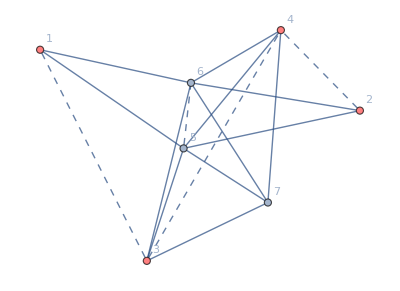

```mathematica
drawGraph[{inthard(*integrand*),{1,2,3,4}(*external vertices*)},"withoutnum"->False(*draw numerators*)]
```

## Section 2: leading singularity analysis

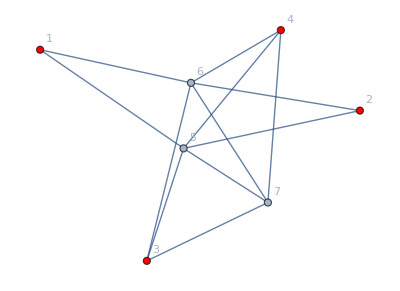
denom graph: -Graphics-

the loop variables are {x_5,x_6,x_7}

Step 1: integrate x_7 first.

Calculating Jacobians for loop: x_7

The four conditions are: {x_(3,7)^2,x_(4,7)^2,x_(5,7)^2,x_(6,7)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(3,4)^2 | -2 x_(3,5)^2 | -2 x_(3,6)^2
-2 x_(3,4)^2 | 0 | -2 x_(4,5)^2 | -2 x_(4,6)^2
-2 x_(3,5)^2 | -2 x_(4,5)^2 | 0 | -2 x_(5,6)^2
-2 x_(3,6)^2 | -2 x_(4,6)^2 | -2 x_(5,6)^2 | 0)

remaining loops: {5,6} length of remaining term: 1

Step 2 : cut the 2nd loop variable.

the 1st cut:

cut {V2[x[1,5]],V2[x[1,6]],V2[x[2,5]],V2[x[2,6]],V2[x[3,5]],V2[x[3,6]],V2[x[4,5]],V2[x[4,6]],λ_{3,4,5,6}} for x_5. numerator: V2[x[1,3]] V2[x[2,4]] V2[x[3,4]] V2[x[5,6]]

totally 5 cases:

case 1: {V2[x[1,5]],V2[x[2,5]],V2[x[3,5]],V2[x[4,5]]}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4} V2[x[1,6]] V2[x[2,6]] V2[x[3,6]] V2[x[4,6]]
V2[x[1,3]] V2[x[2,4]]

case 2: {V2[x[1,5]],V2[x[2,5]],V2[x[3,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(3,6)^2 x_(4,5)^2-x_(3,4)^2 x_(5,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(3,6)^2 x_(4,5)^2-x_(3,4)^2 x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | 2 (x_(1,6)^2 x_(3,4)^2-x_(1,4)^2 x_(3,6)^2)
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,4)^2 x_(3,6)^2)
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | 0
2 (x_(1,6)^2 x_(3,4)^2-x_(1,4)^2 x_(3,6)^2) | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,4)^2 x_(3,6)^2) | 0 | 4 x_(3,4)^2 x_(3,6)^2 x_(4,6)^2)

the remaining expression is 4 λ_{1,2,3,{4,6}} V2[x[1,6]] V2[x[2,6]] V2[x[4,6]]
V2[x[1,3]] V2[x[2,4]]

case 3: {V2[x[1,5]],V2[x[2,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(4,5)^2,x_(3,5)^2 x_(4,6)^2-x_(3,4)^2 x_(5,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(4,5)^2,x_(3,5)^2 x_(4,6)^2-x_(3,4)^2 x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,4)^2 | 2 (x_(1,6)^2 x_(3,4)^2-x_(1,3)^2 x_(4,6)^2)
-2 x_(1,2)^2 | 0 | -2 x_(2,4)^2 | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,3)^2 x_(4,6)^2)
-2 x_(1,4)^2 | -2 x_(2,4)^2 | 0 | 0
2 (x_(1,6)^2 x_(3,4)^2-x_(1,3)^2 x_(4,6)^2) | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,3)^2 x_(4,6)^2) | 0 | 4 x_(3,4)^2 x_(3,6)^2 x_(4,6)^2)

the remaining expression is 4 λ_{1,2,4,{3,6}} V2[x[1,6]] V2[x[2,6]] V2[x[3,6]]
V2[x[1,3]] V2[x[2,4]]

case 4: {V2[x[1,5]],V2[x[3,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}}

the constant term is V2[x[3,4]]

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,3)^2 | -2 x_(1,4)^2 | -2 x_(1,6)^2
-2 x_(1,3)^2 | 0 | -2 x_(3,4)^2 | -2 x_(3,6)^2
-2 x_(1,4)^2 | -2 x_(3,4)^2 | 0 | -2 x_(4,6)^2
-2 x_(1,6)^2 | -2 x_(3,6)^2 | -2 x_(4,6)^2 | 0)

this cut is 0.

case 5: {V2[x[2,5]],V2[x[3,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(2,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}}

the constant term is V2[x[3,4]]

Calculating Jacobians for loop: x_5

The four conditions are: {x_(2,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(2,3)^2 | -2 x_(2,4)^2 | -2 x_(2,6)^2
-2 x_(2,3)^2 | 0 | -2 x_(3,4)^2 | -2 x_(3,6)^2
-2 x_(2,4)^2 | -2 x_(3,4)^2 | 0 | -2 x_(4,6)^2
-2 x_(2,6)^2 | -2 x_(3,6)^2 | -2 x_(4,6)^2 | 0)

this cut is 0.

number of cut got: 3

remaining loops: {6} length of remaining term: 3

Step 3 : cut the 3rd loop variable.

the 1st cut:

cut {λ_{1,2,3,4},V2[x[1,6]],V2[x[2,6]],V2[x[3,6]],V2[x[4,6]]} for x_6. numerator: V2[x[1,3]] V2[x[2,4]]

totally 1 cases:

case 1: {V2[x[1,6]],V2[x[2,6]],V2[x[3,6]],V2[x[4,6]]}

the condition of cuts can be further split into: {{x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4}^2
V2[x[1,3]] V2[x[2,4]]

the 2nd cut:

cut {λ_{1,2,3,{4,6}},V2[x[1,6]],V2[x[2,6]],V2[x[4,6]]} for x_6. numerator: V2[x[1,3]] V2[x[2,4]]

totally 1 cases:

case 1: {λ_{1,2,3,{4,6}},V2[x[1,6]],V2[x[2,6]],V2[x[4,6]]}

the condition of cuts can be further split into: {{x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}}

the constant term is V2[x[1,4]] V2[x[2,3]]-V2[x[1,3]] V2[x[2,4]]

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4} (-V2[x[1,4]] V2[x[2,3]]+V2[x[1,3]] V2[x[2,4]])
-V2[x[1,3]] V2[x[2,4]]

the 3rd cut:

cut {λ_{1,2,4,{3,6}},V2[x[1,6]],V2[x[2,6]],V2[x[3,6]]} for x_6. numerator: V2[x[1,3]] V2[x[2,4]]

totally 1 cases:

case 1: {λ_{1,2,4,{3,6}},V2[x[1,6]],V2[x[2,6]],V2[x[3,6]]}

the condition of cuts can be further split into: {{x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}}

the constant term is V2[x[1,4]] V2[x[2,3]]-V2[x[1,3]] V2[x[2,4]]

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4} (-V2[x[1,4]] V2[x[2,3]]+V2[x[1,3]] V2[x[2,4]])
-V2[x[1,3]] V2[x[2,4]]

number of cut got: 3

Last Step:  expressing the leading singularities with u and v. u=(x_(1,2)^2 x_(3,4)^2)/(x_(1,3)^2 x_(2,4)^2)v=(x_(1,4)^2 x_(2,3)^2)/(x_(1,3)^2 x_(2,4)^2)

{1/((1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]]),-1/((-1+v) √(1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]]),-1/((-1+v) √(1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]])}

```mathematica
LeadingSingularities[inthard]
```

Through this leading singularity analysis, we know if we change the numerator from x[3,4]x[5,6] to x[3,4]x[5,6]-x[3,6]x[4,5]-x[3,5]x[4,6], then the leading singularity of 1/(z-zz)^2 is separated. Then this integrand can be split into two parts:

```mathematica
inthard1=((x[5,6]*x[3,4]-x[3,6]x[4,5]-x[3,5]x[4,6])*(x[1,3]x[2,4])/(x[5,1]x[5,2]x[5,3]x[5,4]x[6,1]x[6,2]x[6,3]x[6,4]x[6,7]x[5,7]x[7,3]x[7,4]))//Factor;
inthard2=inthard-inthard1//Factor;
```

```mathematica
LeadingSingularities[inthard1]
```

denom graph: -Graphics-

the loop variables are {x_5,x_6,x_7}

Step 1: integrate x_7 first.

Calculating Jacobians for loop: x_7

The four conditions are: {x_(3,7)^2,x_(4,7)^2,x_(5,7)^2,x_(6,7)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(3,4)^2 | -2 x_(3,5)^2 | -2 x_(3,6)^2
-2 x_(3,4)^2 | 0 | -2 x_(4,5)^2 | -2 x_(4,6)^2
-2 x_(3,5)^2 | -2 x_(4,5)^2 | 0 | -2 x_(5,6)^2
-2 x_(3,6)^2 | -2 x_(4,6)^2 | -2 x_(5,6)^2 | 0)

remaining loops: {5,6} length of remaining term: 1

Step 2 : cut the 2nd loop variable.

the 1st cut:

cut {V2[x[1,5]],V2[x[1,6]],V2[x[2,5]],V2[x[2,6]],V2[x[3,5]],V2[x[3,6]],V2[x[4,5]],V2[x[4,6]],λ_{3,4,5,6}} for x_5. numerator: -V2[x[1,3]] V2[x[2,4]] (V2[x[3,6]] V2[x[4,5]]+V2[x[3,5]] V2[x[4,6]]-V2[x[3,4]] V2[x[5,6]])

totally 5 cases:

case 1: {V2[x[1,5]],V2[x[2,5]],V2[x[3,5]],V2[x[4,5]]}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4} V2[x[1,6]] V2[x[2,6]] V2[x[3,6]] V2[x[4,6]]
V2[x[1,3]] V2[x[2,4]]

case 2: {V2[x[1,5]],V2[x[2,5]],V2[x[3,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(3,6)^2 x_(4,5)^2-x_(3,4)^2 x_(5,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(3,6)^2 x_(4,5)^2-x_(3,4)^2 x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | 2 (x_(1,6)^2 x_(3,4)^2-x_(1,4)^2 x_(3,6)^2)
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,4)^2 x_(3,6)^2)
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | 0
2 (x_(1,6)^2 x_(3,4)^2-x_(1,4)^2 x_(3,6)^2) | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,4)^2 x_(3,6)^2) | 0 | 4 x_(3,4)^2 x_(3,6)^2 x_(4,6)^2)

this cut is 0.

case 3: {V2[x[1,5]],V2[x[2,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(4,5)^2,x_(3,5)^2 x_(4,6)^2-x_(3,4)^2 x_(5,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(4,5)^2,x_(3,5)^2 x_(4,6)^2-x_(3,4)^2 x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,4)^2 | 2 (x_(1,6)^2 x_(3,4)^2-x_(1,3)^2 x_(4,6)^2)
-2 x_(1,2)^2 | 0 | -2 x_(2,4)^2 | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,3)^2 x_(4,6)^2)
-2 x_(1,4)^2 | -2 x_(2,4)^2 | 0 | 0
2 (x_(1,6)^2 x_(3,4)^2-x_(1,3)^2 x_(4,6)^2) | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,3)^2 x_(4,6)^2) | 0 | 4 x_(3,4)^2 x_(3,6)^2 x_(4,6)^2)

this cut is 0.

case 4: {V2[x[1,5]],V2[x[3,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}}

the constant term is V2[x[3,4]]

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,3)^2 | -2 x_(1,4)^2 | -2 x_(1,6)^2
-2 x_(1,3)^2 | 0 | -2 x_(3,4)^2 | -2 x_(3,6)^2
-2 x_(1,4)^2 | -2 x_(3,4)^2 | 0 | -2 x_(4,6)^2
-2 x_(1,6)^2 | -2 x_(3,6)^2 | -2 x_(4,6)^2 | 0)

this cut is 0.

case 5: {V2[x[2,5]],V2[x[3,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(2,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}}

the constant term is V2[x[3,4]]

Calculating Jacobians for loop: x_5

The four conditions are: {x_(2,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(2,3)^2 | -2 x_(2,4)^2 | -2 x_(2,6)^2
-2 x_(2,3)^2 | 0 | -2 x_(3,4)^2 | -2 x_(3,6)^2
-2 x_(2,4)^2 | -2 x_(3,4)^2 | 0 | -2 x_(4,6)^2
-2 x_(2,6)^2 | -2 x_(3,6)^2 | -2 x_(4,6)^2 | 0)

this cut is 0.

number of cut got: 1

remaining loops: {6} length of remaining term: 1

Step 3 : cut the 3rd loop variable.

the 1st cut:

cut {λ_{1,2,3,4},V2[x[1,6]],V2[x[2,6]],V2[x[3,6]],V2[x[4,6]]} for x_6. numerator: V2[x[1,3]] V2[x[2,4]]

totally 1 cases:

case 1: {V2[x[1,6]],V2[x[2,6]],V2[x[3,6]],V2[x[4,6]]}

the condition of cuts can be further split into: {{x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4}^2
V2[x[1,3]] V2[x[2,4]]

number of cut got: 1

Last Step:  expressing the leading singularities with u and v. u=(x_(1,2)^2 x_(3,4)^2)/(x_(1,3)^2 x_(2,4)^2)v=(x_(1,4)^2 x_(2,3)^2)/(x_(1,3)^2 x_(2,4)^2)

{1/((1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]])}

```mathematica
LeadingSingularities[inthard2]
```

denom graph: -Graphics-

the loop variables are {x_5,x_6,x_7}

Step 1: integrate x_7 first.

Calculating Jacobians for loop: x_7

The four conditions are: {x_(3,7)^2,x_(4,7)^2,x_(5,7)^2,x_(6,7)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(3,4)^2 | -2 x_(3,5)^2 | -2 x_(3,6)^2
-2 x_(3,4)^2 | 0 | -2 x_(4,5)^2 | -2 x_(4,6)^2
-2 x_(3,5)^2 | -2 x_(4,5)^2 | 0 | -2 x_(5,6)^2
-2 x_(3,6)^2 | -2 x_(4,6)^2 | -2 x_(5,6)^2 | 0)

remaining loops: {5,6} length of remaining term: 1

Step 2 : cut the 2nd loop variable.

the 1st cut:

cut {V2[x[1,5]],V2[x[1,6]],V2[x[2,5]],V2[x[2,6]],V2[x[3,5]],V2[x[3,6]],V2[x[4,5]],V2[x[4,6]],λ_{3,4,5,6}} for x_5. numerator: V2[x[1,3]] V2[x[2,4]] (V2[x[3,6]] V2[x[4,5]]+V2[x[3,5]] V2[x[4,6]])

totally 5 cases:

case 1: {V2[x[1,5]],V2[x[2,5]],V2[x[3,5]],V2[x[4,5]]}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

this cut is 0.

case 2: {V2[x[1,5]],V2[x[2,5]],V2[x[3,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(3,6)^2 x_(4,5)^2-x_(3,4)^2 x_(5,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(3,6)^2 x_(4,5)^2-x_(3,4)^2 x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | 2 (x_(1,6)^2 x_(3,4)^2-x_(1,4)^2 x_(3,6)^2)
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,4)^2 x_(3,6)^2)
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | 0
2 (x_(1,6)^2 x_(3,4)^2-x_(1,4)^2 x_(3,6)^2) | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,4)^2 x_(3,6)^2) | 0 | 4 x_(3,4)^2 x_(3,6)^2 x_(4,6)^2)

the remaining expression is 4 λ_{1,2,3,{4,6}} V2[x[1,6]] V2[x[2,6]] V2[x[4,6]]
V2[x[1,3]] V2[x[2,4]]

case 3: {V2[x[1,5]],V2[x[2,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(2,5)^2,x_(4,5)^2,x_(3,5)^2 x_(4,6)^2-x_(3,4)^2 x_(5,6)^2}}

the constant term is 1

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(4,5)^2,x_(3,5)^2 x_(4,6)^2-x_(3,4)^2 x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,4)^2 | 2 (x_(1,6)^2 x_(3,4)^2-x_(1,3)^2 x_(4,6)^2)
-2 x_(1,2)^2 | 0 | -2 x_(2,4)^2 | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,3)^2 x_(4,6)^2)
-2 x_(1,4)^2 | -2 x_(2,4)^2 | 0 | 0
2 (x_(1,6)^2 x_(3,4)^2-x_(1,3)^2 x_(4,6)^2) | 2 (x_(2,6)^2 x_(3,4)^2-x_(2,3)^2 x_(4,6)^2) | 0 | 4 x_(3,4)^2 x_(3,6)^2 x_(4,6)^2)

the remaining expression is 4 λ_{1,2,4,{3,6}} V2[x[1,6]] V2[x[2,6]] V2[x[3,6]]
V2[x[1,3]] V2[x[2,4]]

case 4: {V2[x[1,5]],V2[x[3,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(1,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}}

the constant term is V2[x[3,4]]

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,3)^2 | -2 x_(1,4)^2 | -2 x_(1,6)^2
-2 x_(1,3)^2 | 0 | -2 x_(3,4)^2 | -2 x_(3,6)^2
-2 x_(1,4)^2 | -2 x_(3,4)^2 | 0 | -2 x_(4,6)^2
-2 x_(1,6)^2 | -2 x_(3,6)^2 | -2 x_(4,6)^2 | 0)

this cut is 0.

case 5: {V2[x[2,5]],V2[x[3,5]],V2[x[4,5]],λ_{3,4,5,6}}

the condition of cuts can be further split into: {{x_(2,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}}

the constant term is V2[x[3,4]]

Calculating Jacobians for loop: x_5

The four conditions are: {x_(2,5)^2,x_(3,5)^2,x_(4,5)^2,x_(5,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(2,3)^2 | -2 x_(2,4)^2 | -2 x_(2,6)^2
-2 x_(2,3)^2 | 0 | -2 x_(3,4)^2 | -2 x_(3,6)^2
-2 x_(2,4)^2 | -2 x_(3,4)^2 | 0 | -2 x_(4,6)^2
-2 x_(2,6)^2 | -2 x_(3,6)^2 | -2 x_(4,6)^2 | 0)

this cut is 0.

number of cut got: 2

remaining loops: {6} length of remaining term: 2

Step 3 : cut the 3rd loop variable.

the 1st cut:

cut {λ_{1,2,3,{4,6}},V2[x[1,6]],V2[x[2,6]],V2[x[4,6]]} for x_6. numerator: V2[x[1,3]] V2[x[2,4]]

totally 1 cases:

case 1: {λ_{1,2,3,{4,6}},V2[x[1,6]],V2[x[2,6]],V2[x[4,6]]}

the condition of cuts can be further split into: {{x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}}

the constant term is V2[x[1,4]] V2[x[2,3]]-V2[x[1,3]] V2[x[2,4]]

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4} (-V2[x[1,4]] V2[x[2,3]]+V2[x[1,3]] V2[x[2,4]])
-V2[x[1,3]] V2[x[2,4]]

the 2nd cut:

cut {λ_{1,2,4,{3,6}},V2[x[1,6]],V2[x[2,6]],V2[x[3,6]]} for x_6. numerator: V2[x[1,3]] V2[x[2,4]]

totally 1 cases:

case 1: {λ_{1,2,4,{3,6}},V2[x[1,6]],V2[x[2,6]],V2[x[3,6]]}

the condition of cuts can be further split into: {{x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}}

the constant term is V2[x[1,4]] V2[x[2,3]]-V2[x[1,3]] V2[x[2,4]]

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

the remaining expression is 4 λ_{1,2,3,4} (-V2[x[1,4]] V2[x[2,3]]+V2[x[1,3]] V2[x[2,4]])
-V2[x[1,3]] V2[x[2,4]]

number of cut got: 2

Last Step:  expressing the leading singularities with u and v. u=(x_(1,2)^2 x_(3,4)^2)/(x_(1,3)^2 x_(2,4)^2)v=(x_(1,4)^2 x_(2,3)^2)/(x_(1,3)^2 x_(2,4)^2)

{-1/((-1+v) √(1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]]),-1/((-1+v) √(1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]])}

Now we calculate inthard2 as a simple example, the calculation of inthard1 will be the same. inthard1 will be a little harder.

## Section 3: Construct the ansatz

Let us reduce the original integrals and analyse the leading singularity of reduced graph to guess the letters for our ansatz

```mathematica
GraphReduce[inthard]
```

2 case(s) found after modding the symmetry

{-(x[1,3] x[2,4])/(x[1,5] x[1,6] x[2,5] x[2,6] x[3,5] x[3,6] x[4,5] x[4,6]),(x[1,3] x[2,4])/(x[1,5] x[1,6] x[2,5] x[2,6] x[3,5] x[3,6] x[4,5] x[4,6])}

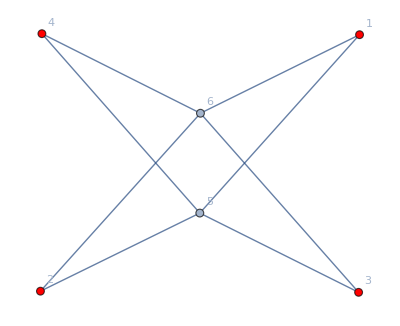
denom graph: -Graphics-

the loop variables are {x_5,x_6}

Step 1: integrate {x_5,x_6} first.

Calculating Jacobians for loop: x_5

The four conditions are: {x_(1,5)^2,x_(2,5)^2,x_(3,5)^2,x_(4,5)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

Calculating Jacobians for loop: x_6

The four conditions are: {x_(1,6)^2,x_(2,6)^2,x_(3,6)^2,x_(4,6)^2}

The corresponding Jacobian matrix is: (0 | -2 x_(1,2)^2 | -2 x_(1,3)^2 | -2 x_(1,4)^2
-2 x_(1,2)^2 | 0 | -2 x_(2,3)^2 | -2 x_(2,4)^2
-2 x_(1,3)^2 | -2 x_(2,3)^2 | 0 | -2 x_(3,4)^2
-2 x_(1,4)^2 | -2 x_(2,4)^2 | -2 x_(3,4)^2 | 0)

Last Step:  expressing the leading singularities with u and v. u=(x_(1,2)^2 x_(3,4)^2)/(x_(1,3)^2 x_(2,4)^2)v=(x_(1,4)^2 x_(2,3)^2)/(x_(1,3)^2 x_(2,4)^2)

{1/((1-2 u+u^2-2 v-2 u v+v^2) V2[x[1,3]] V2[x[2,4]])}

```mathematica
LeadingSingularities[(x[1,3] x[2,4])/(x[1,5] x[1,6] x[2,5] x[2,6] x[3,5] x[3,6] x[4,5] x[4,6])]
```

The leading singularity is 1/(z-zz)^2, it indicate that for our integrals, there should be symbol letter z-zz, or zz should appear in our svmpl basis. Since inthard2 is invariant under  z<->zz, there is a 1/(z-zz) in its leading singularity, so the ansatz we construct should be odd so that it will cancel minus sign from 1/(z-zz) under z<->zz.

### ansatz for SVMPL: parity odd and parity even: zz

We try to construct an odd ansatz for SVMPL with zz

```mathematica
$Letter=zz;
```

For three loop, we construct up to weight 6. If this is a four loop integral, construct it up to weight 8.

```mathematica
(*first is the svhpl, all svhpl up to weight-8 has been constructed*)
allsvlistoddans=Import[FileNameJoin[{dir,"allsvlistoddans.m"}]];
oddansatz=Join[allsvlistoddans[[6]](*weight 6*),f[5]*allsvlistoddans[[1]],f[3]*allsvlistoddans[[3]]];
Length[oddansatz]
```

30

```mathematica
allsvlistevenans=Import[FileNameJoin[{dir,"allsvlistevenans.m"}]];
evenansatz=Join[allsvlistevenans[[6]](*weight 6*),f[5]*allsvlistevenans[[1]],f[3]*allsvlistevenans[[3]]];
Length[evenansatz]
```

44

```mathematica
svlistmplans=Join[f[5]*I[z,Sequence@@#,0]&/@((Tuples[{$Letter,0,1},1](*//DeleteCases[#,_?(FreeQ[#,zz]&)]&*))),f[3]*I[z,Sequence@@#,0]&/@(Outer[Join,(Tuples[{$Letter,0,1},2](*//DeleteCases[#,_?(FreeQ[#,zz]&)]&*)),Tuples[{0,1},1],1]//Flatten[#,1]&),I[z,Sequence@@#,0]&/@(Outer[Join,(Tuples[{$Letter,0,1},2](*//DeleteCases[#,_?(FreeQ[#,zz]&)]&*)),Tuples[{0,1},4],1]//Flatten[#,1]&)];
```

```mathematica
$LENG=svlistmplans//Length
```

165

```mathematica
(*we use hyperlogprocedures to calculate the complex conjugate of the ansatz, you can calculate by yourself or use the results we already have*)
```

```mathematica
svlistmpln=Cases[svlistmplans,_I,Infinity]//DeleteDuplicates;
```

```mathematica
(*adjust the position according to your calculation*)
Export["/Users/windfolgen/Library/CloudStorage/Nutstore-17801035153@163.com/NutFiles/ssvhpl_periods/svlistmplthreeloophard.txt",(svlistmpln//InputForm//ToString)//StringTrim[#,"{"|"}"]&//"["<>#<>"]"&];
```

The following part is calculated following skill files under project_skills/series_expansion/SKILL_hyperlog_conjugate.md.  You can also use the results I calculated here under current folder

```mathematica
svlistmplnconj=If[FileExistsQ["/Users/windfolgen/Library/CloudStorage/Nutstore-17801035153@163.com/NutFiles/ssvhpl_periods/svlistmplthreeloophardconj.txt"],("{"<>(StringDrop[(Import["/Users/windfolgen/Library/CloudStorage/Nutstore-17801035153@163.com/NutFiles/ssvhpl_periods/svlistmplthreeloophardconj.txt"]),1]//StringDrop[#,-1]&)<>"}")//ToExpression,("{"<>(StringDrop[(Import[FileNameJoin[{dir,"svlistmplthreeloophardconj.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression];
```

```mathematica
svlistmpln[[-3]]
```

ⅈ[z,1,1,1,1,0,1,0]

```mathematica
svlistmplnconj[[-3]]
```

ⅈ[z,1,0,1,1,1,1,0]-4 ⅈ[z,1,1,1,0] f[3]-10 ⅈ[z,1,0] f[5]

As you can see, after conjugation, the position of the letter will go to arbitrary position, but we will still require in the ansatz we constructed, these new letters appears in the last two entries, this is why the constraints are so strong for svmpl

```mathematica
conjrep=Thread@Rule[svlistmpln,svlistmplnconj];
```

```mathematica
svlistall=Cases[conjrep,_I,Infinity]//DeleteDuplicates;
```

```mathematica
svlistall//Length
```

558

#### odd ansatz

```mathematica
presys=Last@Normal[CoefficientArrays[(c/@Range[$LENG]).(svlistmplans/.conjrep)+(c/@Range[$LENG]).svlistmplans,svlistall]];
```

```mathematica
presys1=Table[(presys[[i]]/.{Pi->pi,f[3,3]->f[3]^2/2}//MonomialList[#,{f[3],pi,f[5],f[7],f[5,3]}]&)/.{pi->1,f[3]->1,f[5]->1,f[7]->1},{i,1,Length[presys]}]//Flatten;
```

```mathematica
sys=CoefficientArrays[presys1,(c/@Range[$LENG])][[2]];
ns=NullSpace[sys]//RowReduce;
```

```mathematica
ns//Length
```

43

```mathematica
ClearAll[MatchAnsatz];
MatchAnsatz[exp_,ansatz_]:=Module[{svlistall,sys,sys1,len,sol},
svlistall=Cases[ansatz,_I,Infinity]//DeleteDuplicates;
len=Length[ansatz];
sys=CoefficientArrays[-(exp)+(c/@Range[len]).ansatz,svlistall][[2]]//Normal;
sys1=Table[(sys[[i]]/.{Pi->pi,f[3,3]->f[3]^2/2}//MonomialList[#,{f[3],pi,f[5],f[7],f[5,3]}]&)/.{pi->1,f[3]->1,f[5]->1,f[7]->1},{i,1,Length[sys]}]//Flatten;
sol=Solve[Thread@Equal[sys1,0],c/@Range[len]][[1]];
Return[c/@Range[len]/.sol];
];
```

```mathematica
presyst=Table[MatchAnsatz[oddansatz[[i]],svlistmplans],{i,1,Length[oddansatz]}];
```

```mathematica
presyst//Length
```

30

```mathematica
ClearAll[PartialRowReduce];
PartialRowReduce[mat1_,mat2_]:=Module[{tem,temmat,temmat1,rank},
tem=mat1//SortBy[#,LeafCount]&;
temmat=mat2;
rank=MatrixRank[temmat];
Do[
temmat1=Append[temmat,tem[[i]]];
If[MatrixRank[temmat1]-rank==1,temmat=temmat1;rank=rank+1;]
,{i,1,Length[tem]}];
Return[temmat];
];
```

```mathematica
ns1=PartialRowReduce[ns,presyst];
ns1//Length
```

43

```mathematica
Export[FileNameJoin[{dir,"svmploddansatz_threeloop.m"}],Drop[ns1,30].svlistmplans];
```

13 results remain

```mathematica
basis=Import[FileNameJoin[{dir,"svmploddansatz_threeloop.m"}]];
```

```mathematica
basis[[-1]]
```

1/8 ⅈ[z,0,1,0,1,1,0,0]+1/8 ⅈ[z,0,1,1,1,0,1,0]-1/8 ⅈ[z,0,1,1,1,1,0,0]-1/4 ⅈ[z,0,zz,0,1,0,1,0]+1/8 ⅈ[z,0,zz,0,1,1,1,0]+1/4 ⅈ[z,0,zz,1,0,1,0,0]-1/8 ⅈ[z,0,zz,1,0,1,1,0]+1/8 ⅈ[z,0,zz,1,1,0,1,0]-1/8 ⅈ[z,0,zz,1,1,1,0,0]-1/12 ⅈ[z,1,0,1,0,1,1,0]-1/8 ⅈ[z,1,0,1,1,0,1,0]-1/8 ⅈ[z,1,0,1,1,1,0,0]+19/60 ⅈ[z,1,0,1,1,1,1,0]+1/12 ⅈ[z,1,1,0,1,0,1,0]+1/8 ⅈ[z,1,1,0,1,1,0,0]-29/120 ⅈ[z,1,1,0,1,1,1,0]-1/8 ⅈ[z,1,1,1,0,1,0,0]+7/60 ⅈ[z,1,1,1,0,1,1,0]-1/15 ⅈ[z,1,1,1,1,0,1,0]-1/4 ⅈ[z,1,zz,0,1,0,1,0]+1/8 ⅈ[z,1,zz,0,1,1,1,0]+1/4 ⅈ[z,1,zz,1,0,1,0,0]-1/8 ⅈ[z,1,zz,1,0,1,1,0]+1/8 ⅈ[z,1,zz,1,1,0,1,0]-1/8 ⅈ[z,1,zz,1,1,1,0,0]+1/2 ⅈ[z,zz,0,1,0,1,0,0]+1/4 ⅈ[z,zz,0,1,1,0,1,0]-1/4 ⅈ[z,zz,0,1,1,1,0,0]-1/4 ⅈ[z,zz,0,1,1,1,1,0]-1/2 ⅈ[z,zz,1,0,1,0,1,0]-1/4 ⅈ[z,zz,1,0,1,1,0,0]+1/2 ⅈ[z,zz,1,0,1,1,1,0]-1/4 ⅈ[z,zz,1,1,0,1,1,0]+1/4 ⅈ[z,zz,1,1,1,1,0,0]+ⅈ[z,zz,zz,0,1,0,1,0]-1/2 ⅈ[z,zz,zz,0,1,1,1,0]-ⅈ[z,zz,zz,1,0,1,0,0]+1/2 ⅈ[z,zz,zz,1,0,1,1,0]-1/2 ⅈ[z,zz,zz,1,1,0,1,0]+1/2 ⅈ[z,zz,zz,1,1,1,0,0]

#### even ansatz

```mathematica
presys=Last@Normal[CoefficientArrays[(c/@Range[$LENG]).(svlistmplans/.conjrep)-(c/@Range[$LENG]).svlistmplans,svlistall]];
```

```mathematica
presys1=Table[(presys[[i]]/.{Pi->pi,f[3,3]->f[3]^2/2}//MonomialList[#,{f[3],pi,f[5],f[7],f[5,3]}]&)/.{pi->1,f[3]->1,f[5]->1,f[7]->1},{i,1,Length[presys]}]//Flatten;
```

```mathematica
sys=CoefficientArrays[presys1,(c/@Range[$LENG])][[2]];
ns=NullSpace[sys]//RowReduce;
```

```mathematica
ns//Length
```

56

```mathematica
ClearAll[MatchAnsatz];
MatchAnsatz[exp_,ansatz_]:=Module[{svlistall,sys,sys1,len,sol},
svlistall=Cases[ansatz,_I,Infinity]//DeleteDuplicates;
len=Length[ansatz];
sys=CoefficientArrays[-(exp)+(c/@Range[len]).ansatz,svlistall][[2]]//Normal;
sys1=Table[(sys[[i]]/.{Pi->pi,f[3,3]->f[3]^2/2}//MonomialList[#,{f[3],pi,f[5],f[7],f[5,3]}]&)/.{pi->1,f[3]->1,f[5]->1,f[7]->1},{i,1,Length[sys]}]//Flatten;
sol=Solve[Thread@Equal[sys1,0],c/@Range[len]][[1]];
Return[c/@Range[len]/.sol];
];
```

```mathematica
presyst=Table[MatchAnsatz[evenansatz[[i]],svlistmplans],{i,1,Length[evenansatz]}];
```

```mathematica
presyst//Length
```

44

```mathematica
ClearAll[PartialRowReduce];
PartialRowReduce[mat1_,mat2_]:=Module[{tem,temmat,temmat1,rank},
tem=mat1//SortBy[#,LeafCount]&;
temmat=mat2;
rank=MatrixRank[temmat];
Do[
temmat1=Append[temmat,tem[[i]]];
If[MatrixRank[temmat1]-rank==1,temmat=temmat1;rank=rank+1;]
,{i,1,Length[tem]}];
Return[temmat];
];
```

```mathematica
ns1=PartialRowReduce[ns,presyst];
ns1//Length
```

56

```mathematica
Export[FileNameJoin[{dir,"svmplevenansatz_threeloop.m"}],Drop[ns1,44].svlistmplans];
```

12 results remain

```mathematica
Import[FileNameJoin[{dir,"svmplevenansatz_threeloop.m"}]][[-1]]
```

-1/2 ⅈ[z,0,0,1,1,1,0,0]+1/6 ⅈ[z,0,1,0,1,0,0,0]+7/24 ⅈ[z,0,1,1,0,1,0,0]-1/2 ⅈ[z,0,1,1,1,0,0,0]-1/24 ⅈ[z,0,1,1,1,1,0,0]-1/6 ⅈ[z,0,zz,0,0,1,1,0]+1/6 ⅈ[z,0,zz,0,1,1,0,0]-1/8 ⅈ[z,0,zz,0,1,1,1,0]+1/6 ⅈ[z,0,zz,1,0,0,1,0]+1/8 ⅈ[z,0,zz,1,0,1,1,0]-1/6 ⅈ[z,0,zz,1,1,0,0,0]-1/8 ⅈ[z,0,zz,1,1,0,1,0]+1/8 ⅈ[z,0,zz,1,1,1,0,0]-1/6 ⅈ[z,1,0,1,0,0,1,0]+1/6 ⅈ[z,1,0,1,1,0,0,0]-1/6 ⅈ[z,1,1,0,0,1,0,0]-1/6 ⅈ[z,1,1,0,1,0,1,0]+1/8 ⅈ[z,1,1,0,1,1,0,0]-1/8 ⅈ[z,1,1,1,0,1,0,0]+1/8 ⅈ[z,1,1,1,0,1,1,0]-1/6 ⅈ[z,1,zz,0,0,1,1,0]+1/6 ⅈ[z,1,zz,0,1,1,0,0]+1/8 ⅈ[z,1,zz,0,1,1,1,0]+1/6 ⅈ[z,1,zz,1,0,0,1,0]-1/8 ⅈ[z,1,zz,1,0,1,1,0]-1/6 ⅈ[z,1,zz,1,1,0,0,0]+1/8 ⅈ[z,1,zz,1,1,0,1,0]-1/8 ⅈ[z,1,zz,1,1,1,0,0]-1/6 ⅈ[z,zz,0,0,1,0,1,0]+1/6 ⅈ[z,zz,0,0,1,1,0,0]+1/6 ⅈ[z,zz,0,1,0,0,1,0]+1/6 ⅈ[z,zz,0,1,0,1,0,0]-1/6 ⅈ[z,zz,0,1,0,1,1,0]-1/3 ⅈ[z,zz,0,1,1,0,0,0]+1/6 ⅈ[z,zz,0,1,1,0,1,0]+1/6 ⅈ[z,zz,1,0,0,1,0,0]-1/3 ⅈ[z,zz,1,0,0,1,1,0]-1/6 ⅈ[z,zz,1,0,1,0,0,0]+1/6 ⅈ[z,zz,1,0,1,0,1,0]+1/6 ⅈ[z,zz,1,0,1,1,0,0]+1/6 ⅈ[z,zz,1,1,0,0,1,0]-1/6 ⅈ[z,zz,1,1,0,1,0,0]+1/2 ⅈ[z,zz,zz,0,0,1,1,0]-1/2 ⅈ[z,zz,zz,0,1,1,0,0]-1/2 ⅈ[z,zz,zz,1,0,0,1,0]+1/2 ⅈ[z,zz,zz,1,1,0,0,0]+ⅈ[z,1,zz,0,0] f[3]+ⅈ[z,zz,0,1,0] f[3]+ⅈ[z,zz,1,0,0] f[3]

## Section 4: Calculate the boundary condition

Now we calculate the boundary condition using method of region. This has been written as package, you can run it in the current folder asym/ by the script run_**parallel.wl. You can ask your agent learn the structure of the files and write a script for you when you calculate other integrals

### inthard1

```mathematica
inthard1
```

-(x[1,3] x[2,4] (x[3,6] x[4,5]+x[3,5] x[4,6]-x[3,4] x[5,6]))/(x[1,5] x[1,6] x[2,5] x[2,6] x[3,5] x[3,6] x[3,7] x[4,5] x[4,6] x[4,7] x[5,7] x[6,7])

As you can see, there is a factor x[1,3] x[2,4] in the numerator, it will turn into x[1,2]x[3,4] after permutation, which is  u. In that case, we should get the subleading order of u in the expansion, or you can just remove this factor when 2<->3 happens. In that case, do not forget to multiple a v=1-Y, when 1<->2 happens. Here we use the version with x[1,2]x[3,4] multiplied, but for 1324 and 2314 we use numerator with x[1,2]x[3,4] removed, or you can understand it as there is one u removed, these are the O(u) results actually.

For three loops, we only calculate above integrals to O(Y^3) and it finishes in seconds. Now we load them in order

```mathematica
target[1,2,3,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardt1234_order3_asyexp.m"}]]//Normal(*{u,v}*)
```

-20+20 Log[u]-6 Log[u]^2+(2 Log[u]^3)/3+8 Zeta[3]-12 Log[u] Zeta[3]+Y (-10+14 Log[u]-5 Log[u]^2+(2 Log[u]^3)/3+2 Zeta[3]-12 Log[u] Zeta[3])+Y^2 (-7505/1296+(6857 Log[u])/648-(901 Log[u]^2)/216+(67 Log[u]^3)/108-(11 Zeta[3])/9-11 Log[u] Zeta[3])+Y^3 (-4697/1296+(5503 Log[u])/648-(773 Log[u]^2)/216+(31 Log[u]^3)/54-(53 Zeta[3])/18-10 Log[u] Zeta[3])

```mathematica
target[2,1,3,4]=(Import[FileNameJoin[{dirasym,"checkI3Lhardt2134_order3_asyexp.m"}]])//Normal(*{u/v,1/v}*)
```

-20+20 Log[u]-6 Log[u]^2+(2 Log[u]^3)/3+8 Zeta[3]-12 Log[u] Zeta[3]+Y (-10+14 Log[u]-5 Log[u]^2+(2 Log[u]^3)/3+2 Zeta[3]-12 Log[u] Zeta[3])+Y^2 (-7505/1296+(6857 Log[u])/648-(901 Log[u]^2)/216+(67 Log[u]^3)/108-(11 Zeta[3])/9-11 Log[u] Zeta[3])+Y^3 (-4697/1296+(5503 Log[u])/648-(773 Log[u]^2)/216+(31 Log[u]^3)/54-(53 Zeta[3])/18-10 Log[u] Zeta[3])

```mathematica
target[1,3,2,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardt1324_order3_asyexp.m"}]]//Normal(*{1/u,v/u}*)
```

-12+2 Log[u]+Y^3 (-191/288-(11951 Log[u])/5184+(869 Log[u]^2)/864-(59 Log[u]^3)/432-(59 Zeta[3])/9)+Y^2 (-809/432-(2719 Log[u])/1296+(26 Log[u]^2)/27-(13 Log[u]^3)/108-(52 Zeta[3])/9)+Y (-9/2-(5 Log[u])/4+(3 Log[u]^2)/4-Log[u]^3/12-4 Zeta[3])

```mathematica
target[2,3,1,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardt2314_order3_asyexp.m"}]]//Normal(*{v/u,1/u}*)
```

-12+2 Log[u]+Y (-35/2+(21 Log[u])/4-(3 Log[u]^2)/4+Log[u]^3/12+4 Zeta[3])+Y^2 (-7829/432+(7973 Log[u])/1296-(28 Log[u]^2)/27+(7 Log[u]^3)/54+(56 Zeta[3])/9)+Y^3 (-45707/2592+(32863 Log[u])/5184-(985 Log[u]^2)/864+(67 Log[u]^3)/432+(67 Zeta[3])/9)

```mathematica
target[3,1,2,4]=(Import[FileNameJoin[{dirasym,"checkI3Lhardt3124_order3_asyexp.m"}]])//Normal(*{1/v,u/v}*)
```

-12+2 Log[u]+Y^3 (-191/288-(11951 Log[u])/5184+(869 Log[u]^2)/864-(59 Log[u]^3)/432-(59 Zeta[3])/9)+Y^2 (-809/432-(2719 Log[u])/1296+(26 Log[u]^2)/27-(13 Log[u]^3)/108-(52 Zeta[3])/9)+Y (-9/2-(5 Log[u])/4+(3 Log[u]^2)/4-Log[u]^3/12-4 Zeta[3])

```mathematica
target[3,2,1,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardt3214_order3_asyexp.m"}]]//Normal(*{v,u}*)
```

-12+2 Log[u]+Y (-35/2+(21 Log[u])/4-(3 Log[u]^2)/4+Log[u]^3/12+4 Zeta[3])+Y^2 (-7829/432+(7973 Log[u])/1296-(28 Log[u]^2)/27+(7 Log[u]^3)/54+(56 Zeta[3])/9)+Y^3 (-45707/2592+(32863 Log[u])/5184-(985 Log[u]^2)/864+(67 Log[u]^3)/432+(67 Zeta[3])/9)

### inthard2

```mathematica
inthard2
```

(x[1,3] x[2,4] (x[3,6] x[4,5]+x[3,5] x[4,6]))/(x[1,5] x[1,6] x[2,5] x[2,6] x[3,5] x[3,6] x[3,7] x[4,5] x[4,6] x[4,7] x[5,7] x[6,7])

As you can see, there is a factor x[1,3] x[2,4] in the numerator, it will turn into x[1,2]x[3,4] after permutation, which is  u. In that case, we should get the subleading order of u in the expansion, or you can just remove this factor when 2<->3 happens. In that case, do not forget to multiple a v=1-Y, when 1<->2 happens. Here we use the version with x[1,2]x[3,4] multiplied, but for 1324 and 2314 we use numerator with x[1,2]x[3,4] removed, or you can understand it as there is one u removed, these are the O(u) results actually.

For three loops, we only calculate above integrals to O(Y^3) and it finishes in seconds. Now we load them in order

```mathematica
target[1,2,3,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardr1234_order3_asyexp.m"}]]//Normal(*{u,v}*)
```

20-20 Log[u]+6 Log[u]^2-(2 Log[u]^3)/3+4 Zeta[3]+Y^3 (5399/1296-(5611 Log[u])/648+(773 Log[u]^2)/216-(31 Log[u]^3)/54+(31 Zeta[3])/9)+Y^2 (7883/1296-(6911 Log[u])/648+(901 Log[u]^2)/216-(67 Log[u]^3)/108+(67 Zeta[3])/18)+Y (10-14 Log[u]+5 Log[u]^2-(2 Log[u]^3)/3+4 Zeta[3])

```mathematica
target[2,1,3,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardr2134_order3_asyexp.m"}]]//Normal(*{u/v,1/v}*)
```

20-20 Log[u]+6 Log[u]^2-(2 Log[u]^3)/3+Y (-10+6 Log[u]-Log[u]^2)+Y^2 (-5077/1296+(2161 Log[u])/648-(179 Log[u]^2)/216+(5 Log[u]^3)/108-(5 Zeta[3])/18)+Y^3 (-23/12+(325 Log[u])/162-(16 Log[u]^2)/27+(5 Log[u]^3)/108-(5 Zeta[3])/18)+4 Zeta[3]

```mathematica
Import[FileNameJoin[{dirasym,"checkI3Lhardr1324_order3_asyexp.m"}]]//Normal
```

0

```mathematica
target[1,3,2,4]=Import[FileNameJoin[{dirasym,"checkI3Lhard1324_order3_asyexp.m"}]]//Normal(*{1/u,v/u}*)
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3+Y (215/8-(119 Log[u])/8+(13 Log[u]^2)/4-(7 Log[u]^3)/24-14 Zeta[3])+Y^2 (29339/1458-(22957 Log[u])/1944+(1751 Log[u]^2)/648-(161 Log[u]^3)/648-(322 Zeta[3])/27)+Y^3 (6026015/373248-(613685 Log[u])/62208+(12061 Log[u]^2)/5184-(1117 Log[u]^3)/5184-(1117 Zeta[3])/108)-16 Zeta[3]

```mathematica
Import[FileNameJoin[{dirasym,"checkI3Lhardr2314_order3_asyexp.m"}]]//Normal
```

0

```mathematica
target[2,3,1,4]=Import[FileNameJoin[{dirasym,"checkI3Lhard2314_order3_asyexp.m"}]]//Normal(*{v/u,1/u}*)
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3+Y (265/8-(137 Log[u])/8+(15 Log[u]^2)/4-(3 Log[u]^3)/8-18 Zeta[3])+Y^2 (82735/2916-(14273 Log[u])/972+(539 Log[u]^2)/162-(121 Log[u]^3)/324-(484 Zeta[3])/27)+Y^3 (3122795/124416-(268025 Log[u])/20736+(5125 Log[u]^2)/1728-(625 Log[u]^3)/1728-(625 Zeta[3])/36)-16 Zeta[3]

```mathematica
target[3,1,2,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardr3124_order3_asyexp.m"}]]//Normal(*{1/v,u/v}*)
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3-16 Zeta[3]+Y^3 (-494923/124416+(40313 Log[u])/20736-(649 Log[u]^2)/1728+(19 Log[u]^3)/576+(19 Zeta[3])/12)+Y (-105/8+(41 Log[u])/8-(3 Log[u]^2)/4+Log[u]^3/24+2 Zeta[3])+Y^2 (-39379/5832+(745 Log[u])/243-(355 Log[u]^2)/648+(7 Log[u]^3)/162+(56 Zeta[3])/27)

```mathematica
target[3,2,1,4]=Import[FileNameJoin[{dirasym,"checkI3Lhardr3214_order3_asyexp.m"}]]//Normal(*{v,u}*)
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3+Y (265/8-(137 Log[u])/8+(15 Log[u]^2)/4-(3 Log[u]^3)/8-18 Zeta[3])+Y^2 (82735/2916-(14273 Log[u])/972+(539 Log[u]^2)/162-(121 Log[u]^3)/324-(484 Zeta[3])/27)+Y^3 (3122795/124416-(268025 Log[u])/20736+(5125 Log[u]^2)/1728-(625 Log[u]^3)/1728-(625 Zeta[3])/36)-16 Zeta[3]

## Section 5: Calculate the expansion of ansatz

Now since we know the leading singularity is 1/(z-zz)/(1-v), then we need to expand our ansatz to the same O(u^0,Y^3) to match the boundary condition we calculated in the last section

First, we need to expand all single-valued integrals involved in our ansatz with respect to z,zz up to some order in maple. Then we transform the expansion with respect to z,zz to expansion with respect to u and v in this Mathematica notebook.

Same as before, we have calculated the expansion of all svmpls up to weight 8 in Maple (You can also calculate them using your agents). Here we just load them. So the first step is already done.

```mathematica
allsvlist=Table[(I[z,Sequence@@#,0]&/@Tuples[{0,1},i]),{i,1,8}]//Flatten;
```

```mathematica
svliste0=("{"<>(StringDrop[(Import[FileNameJoin[{dir,"allsvliste0_uptow8.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression;
svliste1=("{"<>(StringDrop[(Import[FileNameJoin[{dir,"allsvliste1_uptow8.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression;
svlisteinf=("{"<>(StringDrop[(Import[FileNameJoin[{dir,"allsvlisteinf_uptow8.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression;
```

```mathematica
basisodd=Import[FileNameJoin[{dir,"svmploddansatz_threeloop.m"}]];
basiseven=Import[FileNameJoin[{dir,"svmplevenansatz_threeloop.m"}]];
```

```mathematica
allsvlistmpl=Cases[Join[basisodd,basiseven],_I,Infinity]//DeleteDuplicates//DeleteCases[#,_?(FreeQ[#,zz]&)]&;
```

```mathematica
allsvlistmpl//Length
```

82

```mathematica
Export[FileNameJoin[{dir,"allsvlist_fourloop.m"}],allsvlist];
Export[FileNameJoin[{dir,"allsvlistmpl_threeloop.m"}],allsvlistmpl];
```

```mathematica
(*we export them to some folder where agent can calculate it, you can adjust this folder on your own*)
Export["/Users/windfolgen/Library/CloudStorage/Nutstore-17801035153@163.com/NutFiles/ssvhpl_periods/allsvlistmpl_threeloophard.txt",(allsvlistmpl//InputForm//ToString)//StringTrim[#,"{"|"}"]&//"["<>#<>"]"&];
```

```mathematica
svlistmple0=("{"<>(StringDrop[(Import[FileNameJoin[{dir,"allsvlistmpl_threeloopharde0.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression;
svlistmple1=("{"<>(StringDrop[(Import[FileNameJoin[{dir,"allsvlistmpl_threeloopharde1.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression;
svlistmpleinf=("{"<>(StringDrop[(Import[FileNameJoin[{dir,"allsvlistmpl_threeloophardeinf.txt"}]]),1]//StringDrop[#,-1]&)<>"}")//ToExpression;
```

### series expansion for 1/(z-zz)/(1-v)(a little tedious, more proper for your agent)

```mathematica
Solve[{1/u==z*zz,v/u==(1-z)*(1-zz)},{z,zz}]
```

{{z→(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u),zz→(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u)},{z→(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u),zz→(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

1/(1-v) under the transformation will become u/(u-v), but we will remove an overall u from expression, so the additional factor is 1/(u-v)

```mathematica
svlisteinfuv=SeriesExpansionInf[svlisteinf,zrep,"Yorder"->4,"additional"->1/(u-v)];
svlistmpleinfuv=SeriesExpansionInf[svlistmpleinf,zrep,"Yorder"->4,"additional"->1/(u-v)];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svlisteinfuv.m"}],svlisteinfuv];
Export[FileNameJoin[{dir,"threeloophard_svlistmpleinfuv.m"}],svlistmpleinfuv];
```

```mathematica
Solve[{v/u==z*zz,1/u==(1-z)*(1-zz)},{z,zz}]
```

{{z→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u),zz→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u)},{z→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u),zz→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

1/(1-v) under the transformation will become u/(u-1), but we will remove an overall u from expression, so the additional factor is 1/(u-v)

```mathematica
svlisteinfuvp=SeriesExpansionInfP[svlisteinf,zrep,"Yorder"->4,"additional"->1/(u-1)];
svlistmpleinfuvp=SeriesExpansionInfP[svlistmpleinf,zrep,"Yorder"->4,"additional"->1/(u-1)];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svlisteinfuvp.m"}],svlisteinfuvp];
Export[FileNameJoin[{dir,"threeloophard_svlistmpleinfuvp.m"}],svlistmpleinfuvp];
```

```mathematica
Solve[{u==z*zz,v==(1-z)*(1-zz)},{z,zz}]
```

{{z→1/2 (1+u-√(-4 u+(1+u-v)^2)-v),zz→1/2 (1+u+√(-4 u+(1+u-v)^2)-v)},{z→1/2 (1+u+√(-4 u+(1+u-v)^2)-v),zz→1/2 (1+u-√(-4 u+(1+u-v)^2)-v)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[1/2 (1+u-√(-4 u+(1+u-v)^2)-v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[1/2 (1+u+√(-4 u+(1+u-v)^2)-v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste0uv=SeriesExpansion0[svliste0,zrep,"Yorder"->4,"additional"->1/(1-v)];
svlistmple0uv=SeriesExpansion0[svlistmple0,zrep,"Yorder"->4,"additional"->1/(1-v)];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste0uv.m"}],svliste0uv];
Export[FileNameJoin[{dir,"threeloophard_svlistmple0uv.m"}],svlistmple0uv];
```

```mathematica
Solve[{u/v==z*zz,1/v==(1-z)*(1-zz)},{z,zz}]
```

{{z→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v),zz→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v)},{z→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v),zz→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste0uvp=SeriesExpansion0P[svliste0,zrep,"Yorder"->4,"additional"->v/(v-1)];
svlistmple0uvp=SeriesExpansion0P[svlistmple0,zrep,"Yorder"->4,"additional"->v/(v-1)];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste0uvp.m"}],svliste0uvp];
Export[FileNameJoin[{dir,"threeloophard_svlistmple0uvp.m"}],svlistmple0uvp];
```

```mathematica
Solve[{1/v==z*zz,u/v==(1-z)*(1-zz)},{z,zz}]
```

{{z→(1-u-√((-1+u-v)^2-4 v)+v)/(2 v),zz→(1-u+√((-1+u-v)^2-4 v)+v)/(2 v)},{z→(1-u+√((-1+u-v)^2-4 v)+v)/(2 v),zz→(1-u-√((-1+u-v)^2-4 v)+v)/(2 v)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(1-u-√((-1+u-v)^2-4 v)+v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(1-u+√((-1+u-v)^2-4 v)+v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[z1,i]->(Power[(1-u-√((-1+u-v)^2-4 v)-v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz1,i]->(Power[(1-u+√((-1+u-v)^2-4 v)-v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste1uv=SeriesExpansion1[svliste1,zrep,"Yorder"->4,"additional"->v/(v-u)];
svlistmple1uv=SeriesExpansion1[svlistmple1,zrep,"Yorder"->4,"additional"->v/(v-u)];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste1uv.m"}],svliste1uv];
Export[FileNameJoin[{dir,"threeloophard_svlistmple1uv.m"}],svlistmple1uv];
```

```mathematica
Solve[{v==z*zz,u==(1-z)*(1-zz)},{z,zz}]
```

{{z→1/2 (1-u+v-√(-4 v+(1-u+v)^2)),zz→1/2 (1-u+v+√(-4 v+(1-u+v)^2))},{z→1/2 (1-u+v+√(-4 v+(1-u+v)^2)),zz→1/2 (1-u+v-√(-4 v+(1-u+v)^2))}}

```mathematica
zrep=Table[{Power[z,i]->(Power[1/2 (1-u+v-√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[1/2 (1-u+v+√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[z1,i]->(Power[1/2 (-1-u+v-√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz1,i]->(Power[1/2 (-1-u+v+√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste1uvp=SeriesExpansion1P[svliste1,zrep,"Yorder"->4,"additional"->1/(1-u)];
svlistmple1uvp=SeriesExpansion1P[svlistmple1,zrep,"Yorder"->4,"additional"->1/(1-u)];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste1uvp.m"}],svliste1uvp];
Export[FileNameJoin[{dir,"threeloophard_svlistmple1uvp.m"}],svlistmple1uvp];
```

### series expansion for 1/(z-zz)^2 (a little tedious, more proper for your agent)

```mathematica
Solve[{1/u==z*zz,v/u==(1-z)*(1-zz)},{z,zz}]
```

{{z→(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u),zz→(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u)},{z→(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u),zz→(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(1+u-v-√(-4 u+(-1-u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(1+u-v+√(-4 u+(-1-u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svlisteinfuv2=SeriesExpansion2Inf[svlisteinf,zrep,"Yorder"->4,"additional"->1];
svlistmpleinfuv2=SeriesExpansion2Inf[svlistmpleinf,zrep,"Yorder"->4,"additional"->1];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svlisteinfuv_2.m"}],svlisteinfuv2];
Export[FileNameJoin[{dir,"threeloophard_svlistmpleinfuv_2.m"}],svlistmpleinfuv2];
```

```mathematica
Solve[{v/u==z*zz,1/u==(1-z)*(1-zz)},{z,zz}]
```

{{z→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u),zz→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u)},{z→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u),zz→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 u),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svlisteinfuvp2=SeriesExpansion2InfP[svlisteinf,zrep,"Yorder"->4,"additional"->1];
svlistmpleinfuvp2=SeriesExpansion2InfP[svlistmpleinf,zrep,"Yorder"->4,"additional"->1];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svlisteinfuvp_2.m"}],svlisteinfuvp2];
Export[FileNameJoin[{dir,"threeloophard_svlistmpleinfuvp_2.m"}],svlistmpleinfuvp2];
```

```mathematica
Solve[{u==z*zz,v==(1-z)*(1-zz)},{z,zz}]
```

{{z→1/2 (1+u-√(-4 u+(1+u-v)^2)-v),zz→1/2 (1+u+√(-4 u+(1+u-v)^2)-v)},{z→1/2 (1+u+√(-4 u+(1+u-v)^2)-v),zz→1/2 (1+u-√(-4 u+(1+u-v)^2)-v)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[1/2 (1+u-√(-4 u+(1+u-v)^2)-v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[1/2 (1+u+√(-4 u+(1+u-v)^2)-v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste0uv2=SeriesExpansion20[svliste0,zrep,"Yorder"->4,"additional"->1];
svlistmple0uv2=SeriesExpansion20[svlistmple0,zrep,"Yorder"->4,"additional"->1];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste0uv_2.m"}],svliste0uv2];
Export[FileNameJoin[{dir,"threeloophard_svlistmple0uv_2.m"}],svlistmple0uv2];
```

```mathematica
Solve[{u/v==z*zz,1/v==(1-z)*(1-zz)},{z,zz}]
```

{{z→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v),zz→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v)},{z→(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v),zz→(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(-1+u+v-√(-4 u v+(-1+u+v)^2))/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(-1+u+v+√(-4 u v+(-1+u+v)^2))/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste0uvp2=SeriesExpansion20P[svliste0,zrep,"Yorder"->4,"additional"->1];
svlistmple0uvp2=SeriesExpansion20P[svlistmple0,zrep,"Yorder"->4,"additional"->1];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste0uvp_2.m"}],svliste0uvp2];
Export[FileNameJoin[{dir,"threeloophard_svlistmple0uvp_2.m"}],svlistmple0uvp2];
```

```mathematica
Solve[{1/v==z*zz,u/v==(1-z)*(1-zz)},{z,zz}]
```

{{z→(1-u-√((-1+u-v)^2-4 v)+v)/(2 v),zz→(1-u+√((-1+u-v)^2-4 v)+v)/(2 v)},{z→(1-u+√((-1+u-v)^2-4 v)+v)/(2 v),zz→(1-u-√((-1+u-v)^2-4 v)+v)/(2 v)}}

```mathematica
zrep=Table[{Power[z,i]->(Power[(1-u-√((-1+u-v)^2-4 v)+v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[(1-u+√((-1+u-v)^2-4 v)+v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[z1,i]->(Power[(1-u-√((-1+u-v)^2-4 v)-v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz1,i]->(Power[(1-u+√((-1+u-v)^2-4 v)-v)/(2 v),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste1uv2=SeriesExpansion21[svliste1,zrep,"Yorder"->4,"additional"->1];
svlistmple1uv2=SeriesExpansion21[svlistmple1,zrep,"Yorder"->4,"additional"->1];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste1uv_2.m"}],svliste1uv2];
Export[FileNameJoin[{dir,"threeloophard_svlistmple1uv_2.m"}],svlistmple1uv2];
```

```mathematica
Solve[{v==z*zz,u==(1-z)*(1-zz)},{z,zz}]
```

{{z→1/2 (1-u+v-√(-4 v+(1-u+v)^2)),zz→1/2 (1-u+v+√(-4 v+(1-u+v)^2))},{z→1/2 (1-u+v+√(-4 v+(1-u+v)^2)),zz→1/2 (1-u+v-√(-4 v+(1-u+v)^2))}}

```mathematica
zrep=Table[{Power[z,i]->(Power[1/2 (1-u+v-√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz,i]->(Power[1/2 (1-u+v+√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[z1,i]->(Power[1/2 (-1-u+v-√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&),Power[zz1,i]->(Power[1/2 (-1-u+v+√(-4 v+(1-u+v)^2)),i]/.{v->1-Y}//Expand//Collect[#,Power[_,1/2],Factor]&)},{i,1,10}]//Flatten;
```

```mathematica
svliste1uvp2=SeriesExpansion21P[svliste1,zrep,"Yorder"->4,"additional"->1];
svlistmple1uvp2=SeriesExpansion21P[svlistmple1,zrep,"Yorder"->4,"additional"->1];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard_svliste1uvp_2.m"}],svliste1uvp2];
Export[FileNameJoin[{dir,"threeloophard_svlistmple1uvp_2.m"}],svlistmple1uvp2];
```

### load the results (you can directly load the result if you do not want to calculate the last step)

```mathematica
(*for the leading singularity 1/(z-zz)/(1-v)*)
```

```mathematica
svlisteinfuv=Import[FileNameJoin[{dir,"threeloophard_svlisteinfuv.m"}]];
svlistmpleinfuv=Import[FileNameJoin[{dir,"threeloophard_svlistmpleinfuv.m"}]];
svlisteinfuvp=Import[FileNameJoin[{dir,"threeloophard_svlisteinfuvp.m"}]];
svlistmpleinfuvp=Import[FileNameJoin[{dir,"threeloophard_svlistmpleinfuvp.m"}]];
svliste0uv=Import[FileNameJoin[{dir,"threeloophard_svliste0uv.m"}]];
svlistmple0uv=Import[FileNameJoin[{dir,"threeloophard_svlistmple0uv.m"}]];
svliste0uvp=Import[FileNameJoin[{dir,"threeloophard_svliste0uvp.m"}]];
svlistmple0uvp=Import[FileNameJoin[{dir,"threeloophard_svlistmple0uvp.m"}]];
svliste1uv=Import[FileNameJoin[{dir,"threeloophard_svliste1uv.m"}]];
svlistmple1uv=Import[FileNameJoin[{dir,"threeloophard_svlistmple1uv.m"}]];
svliste1uvp=Import[FileNameJoin[{dir,"threeloophard_svliste1uvp.m"}]];
svlistmple1uvp=Import[FileNameJoin[{dir,"threeloophard_svlistmple1uvp.m"}]];
```

```mathematica
(*for the leading singularity 1/(z-zz)^2*)
```

```mathematica
svlisteinfuv2=Import[FileNameJoin[{dir,"threeloophard_svlisteinfuv_2.m"}]];
svlistmpleinfuv2=Import[FileNameJoin[{dir,"threeloophard_svlistmpleinfuv_2.m"}]];
svlisteinfuvp2=Import[FileNameJoin[{dir,"threeloophard_svlisteinfuvp_2.m"}]];
svlistmpleinfuvp2=Import[FileNameJoin[{dir,"threeloophard_svlistmpleinfuvp_2.m"}]];
svliste0uv2=Import[FileNameJoin[{dir,"threeloophard_svliste0uv_2.m"}]];
svlistmple0uv2=Import[FileNameJoin[{dir,"threeloophard_svlistmple0uv_2.m"}]];
svliste0uvp2=Import[FileNameJoin[{dir,"threeloophard_svliste0uvp_2.m"}]];
svlistmple0uvp2=Import[FileNameJoin[{dir,"threeloophard_svlistmple0uvp_2.m"}]];
svliste1uv2=Import[FileNameJoin[{dir,"threeloophard_svliste1uv_2.m"}]];
svlistmple1uv2=Import[FileNameJoin[{dir,"threeloophard_svlistmple1uv_2.m"}]];
svliste1uvp2=Import[FileNameJoin[{dir,"threeloophard_svliste1uvp_2.m"}]];
svlistmple1uvp2=Import[FileNameJoin[{dir,"threeloophard_svlistmple1uvp_2.m"}]];
```

## section 6: determined all parameters

### inthard1

We first load some integrals calculated.

```mathematica
allsvlist=Import[FileNameJoin[{dir,"allsvlist_fourloop.m"}]];
allsvlistmpl=Import[FileNameJoin[{dir,"allsvlistmpl_threeloop.m"}]];
```

```mathematica
allsvlistevenans=Import[FileNameJoin[{dir,"allsvlistevenans.m"}]];
```

Then construct the ansatz

```mathematica
svhplansatz=Join[allsvlistevenans[[6]](*weight 6*),f[5]*allsvlistevenans[[1]],f[3]*allsvlistevenans[[3]],{f[3,3]}];(*svhpl*)
svmplbasis=Import[FileNameJoin[{dir,"svmplevenansatz_threeloop.m"}]];(*svmpl*)
```

```mathematica
testansatz=Join[svhplansatz,svmplbasis];
$LEN=Length[testansatz]
```

57

```mathematica
$Order=3;(*expansion order of Y*)
```

```mathematica
(*order 1234, {u,v}*)
```

```mathematica
target[1,2,3,4]
```

-20+20 Log[u]-6 Log[u]^2+(2 Log[u]^3)/3+8 Zeta[3]-12 Log[u] Zeta[3]+Y (-10+14 Log[u]-5 Log[u]^2+(2 Log[u]^3)/3+2 Zeta[3]-12 Log[u] Zeta[3])+Y^2 (-7505/1296+(6857 Log[u])/648-(901 Log[u]^2)/216+(67 Log[u]^3)/108-(11 Zeta[3])/9-11 Log[u] Zeta[3])+Y^3 (-4697/1296+(5503 Log[u])/648-(773 Log[u]^2)/216+(31 Log[u]^3)/54-(53 Zeta[3])/18-10 Log[u] Zeta[3])

```mathematica
svrep1=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste0uv2],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple0uv2]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.svrep1;
```

```mathematica
temp=MonomialList[(setup-target[1,2,3,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp//Length
```

7

```mathematica
temp1=Table[(temp[[i]]/.{Log[u]->1,Power[Y,-1]->invY,Power[u,-1]->invu,Power[Y,a_/;(a<0)]:>Power[invY,-a],Power[u,a_/;(a<0)]:>Power[invu,-a]}//MonomialList[#,{u,Y,invY,invu}]&)/.{Y->1,invY->1,invu->1,f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]},{i,1,Length[temp]}];
```

```mathematica
sys=Table[Table[Thread@Equal[MonomialList[temp1[[j]][[i]]/.{Zeta[3]->z3,Zeta[5]->z5,Zeta[7]->z7,Pi->pi},{z3,z5,z7,f[5,3],pi}]/.{z3->1,z5->1,z7->1,f[5,3]->1,pi->1}//DeleteDuplicates//DeleteCases[#,0]&,0],{i,1,Length[temp1[[j]]]}]//Flatten,{j,1,Length[temp1]}]//Flatten//DeleteCases[#,True]&;
```

```mathematica
sol=Solve[sys,Variables[sys[[All,1]]]][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
sol//Length
```

35

```mathematica
(*order 2134, {u/v,1/v}*)
```

```mathematica
target[2,1,3,4]
```

-20+20 Log[u]-6 Log[u]^2+(2 Log[u]^3)/3+8 Zeta[3]-12 Log[u] Zeta[3]+Y (-10+14 Log[u]-5 Log[u]^2+(2 Log[u]^3)/3+2 Zeta[3]-12 Log[u] Zeta[3])+Y^2 (-7505/1296+(6857 Log[u])/648-(901 Log[u]^2)/216+(67 Log[u]^3)/108-(11 Zeta[3])/9-11 Log[u] Zeta[3])+Y^3 (-4697/1296+(5503 Log[u])/648-(773 Log[u]^2)/216+(31 Log[u]^3)/54-(53 Zeta[3])/18-10 Log[u] Zeta[3])

```mathematica
svrep1p=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste0uvp2],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple0uvp2]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.sol/.svrep1p;
```

```mathematica
temp=MonomialList[(setup-target[2,1,3,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

Because we construct the odd ansatz, exchange of 1<->2 gives no new information

```mathematica
(*order 1324, {1/u,v/u}*)(*leading order in u is 0, so we must go to next order in u*)
```

```mathematica
target[1,3,2,4]
```

-12+2 Log[u]+Y^3 (-191/288-(11951 Log[u])/5184+(869 Log[u]^2)/864-(59 Log[u]^3)/432-(59 Zeta[3])/9)+Y^2 (-809/432-(2719 Log[u])/1296+(26 Log[u]^2)/27-(13 Log[u]^3)/108-(52 Zeta[3])/9)+Y (-9/2-(5 Log[u])/4+(3 Log[u]^2)/4-Log[u]^3/12-4 Zeta[3])

```mathematica
svrep2=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svlisteinfuv2],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmpleinfuv2]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.sol/.svrep2;
```

```mathematica
temp=MonomialList[(setup-target[1,3,2,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp//Length
```

7

```mathematica
temp1=Table[(temp[[i]]/.{Log[u]->1,Power[Y,-1]->invY,Power[u,-1]->invu,Power[Y,a_/;(a<0)]:>Power[invY,-a],Power[u,a_/;(a<0)]:>Power[invu,-a]}//MonomialList[#,{u,Y,invY,invu}]&)/.{Y->1,invY->1,invu->1,f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]},{i,1,Length[temp]}];
```

```mathematica
sys1=Table[Table[Thread@Equal[MonomialList[temp1[[j]][[i]]/.{Zeta[3]->z3,Zeta[5]->z5,Zeta[7]->z7,Pi->pi},{z3,z5,z7,f[5,3],pi}]/.{z3->1,z5->1,z7->1,f[5,3]->1,pi->1}//DeleteDuplicates//DeleteCases[#,0]&,0],{i,1,Length[temp1[[j]]]}]//Flatten,{j,1,Length[temp1]}]//Flatten//DeleteCases[#,True]&;
```

```mathematica
Variables[sys1[[All,1]]](*remaining variables*)
```

{c[9],c[10],c[11],c[16],c[17],c[18],c[19],c[20],c[21],c[22],c[23],c[27],c[28],c[29],c[30],c[31],c[32],c[33],c[34],c[36],c[46],c[52]}

```mathematica
syst=Join[sys,sys1];
solt=Solve[syst,Variables[syst[[All,1]]]][[1]];
```

```mathematica
solt
```

{c[1]→0,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→8,c[7]→0,c[8]→-4,c[9]→0,c[10]→-8,c[11]→4,c[12]→0,c[13]→-4,c[14]→4,c[15]→0,c[16]→-8,c[17]→-8,c[18]→20,c[19]→-4,c[20]→-4,c[21]→-2,c[22]→-12,c[23]→0,c[24]→2,c[25]→4,c[26]→0,c[27]→0,c[28]→12,c[29]→4,c[30]→-4,c[31]→6,c[32]→-2,c[33]→0,c[34]→0,c[35]→0,c[36]→0,c[37]→0,c[38]→0,c[39]→0,c[40]→0,c[41]→0,c[42]→-32,c[43]→-16,c[44]→8,c[45]→0,c[46]→0,c[47]→0,c[48]→0,c[49]→0,c[50]→0,c[51]→0,c[52]→0,c[53]→0,c[54]→8,c[55]→-16,c[56]→64,c[57]→0}

The ansatz has been solved here already, but we check all the remaining conditions

```mathematica
(*order 2314, {v/u,1/u}*)(*leading order in u is 0, so we must go to next order in u*)
```

```mathematica
target[2,3,1,4]
```

-12+2 Log[u]+Y (-35/2+(21 Log[u])/4-(3 Log[u]^2)/4+Log[u]^3/12+4 Zeta[3])+Y^2 (-7829/432+(7973 Log[u])/1296-(28 Log[u]^2)/27+(7 Log[u]^3)/54+(56 Zeta[3])/9)+Y^3 (-45707/2592+(32863 Log[u])/5184-(985 Log[u]^2)/864+(67 Log[u]^3)/432+(67 Zeta[3])/9)

```mathematica
svrep2p=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svlisteinfuvp2],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmpleinfuvp2]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.solt/.svrep2p;
```

```mathematica
temp=MonomialList[(setup-target[2,3,1,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

```mathematica
(*order 3124, {1/v,u/v}*)
```

```mathematica
target[3,1,2,4]
```

-12+2 Log[u]+Y^3 (-191/288-(11951 Log[u])/5184+(869 Log[u]^2)/864-(59 Log[u]^3)/432-(59 Zeta[3])/9)+Y^2 (-809/432-(2719 Log[u])/1296+(26 Log[u]^2)/27-(13 Log[u]^3)/108-(52 Zeta[3])/9)+Y (-9/2-(5 Log[u])/4+(3 Log[u]^2)/4-Log[u]^3/12-4 Zeta[3])

```mathematica
svrep3=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste1uv2],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple1uv2]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.solt/.svrep3;
```

```mathematica
temp=MonomialList[(setup-target[3,1,2,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

So this serves as a consistency check of the results bootstrapped

```mathematica
(*order 3214, {v,u}*)
```

```mathematica
target[3,2,1,4]
```

-12+2 Log[u]+Y (-35/2+(21 Log[u])/4-(3 Log[u]^2)/4+Log[u]^3/12+4 Zeta[3])+Y^2 (-7829/432+(7973 Log[u])/1296-(28 Log[u]^2)/27+(7 Log[u]^3)/54+(56 Zeta[3])/9)+Y^3 (-45707/2592+(32863 Log[u])/5184-(985 Log[u]^2)/864+(67 Log[u]^3)/432+(67 Zeta[3])/9)

```mathematica
svrep3p=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste1uvp2],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple1uvp2]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.solt/.svrep3p;
```

```mathematica
temp=MonomialList[(setup-target[3,2,1,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

```mathematica
Export[FileNameJoin[{dir,"threeloophard1_sol.m"}],solt];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard1_ans.m"}],testansatz];
```

### inthard2

We first load some integrals calculated.

```mathematica
allsvlist=Import[FileNameJoin[{dir,"allsvlist_fourloop.m"}]];
allsvlistmpl=Import[FileNameJoin[{dir,"allsvlistmpl_threeloop.m"}]];
```

```mathematica
allsvlistoddans=Import[FileNameJoin[{dir,"allsvlistoddans.m"}]];
```

Then construct the ansatz

```mathematica
svhplansatz=Join[allsvlistoddans[[6]](*weight 6*),f[5]*allsvlistoddans[[1]],f[3]*allsvlistoddans[[3]]];(*svhpl*)
svmplbasis=Import[FileNameJoin[{dir,"svmploddansatz_threeloop.m"}]];(*svmpl*)
```

```mathematica
testansatz=Join[svhplansatz,svmplbasis];
$LEN=Length[testansatz]
```

43

```mathematica
$Order=3;(*expansion order of Y*)
```

```mathematica
(*order 1234, {u,v}*)
```

```mathematica
target[1,2,3,4]
```

20-20 Log[u]+6 Log[u]^2-(2 Log[u]^3)/3+4 Zeta[3]+Y^3 (5399/1296-(5611 Log[u])/648+(773 Log[u]^2)/216-(31 Log[u]^3)/54+(31 Zeta[3])/9)+Y^2 (7883/1296-(6911 Log[u])/648+(901 Log[u]^2)/216-(67 Log[u]^3)/108+(67 Zeta[3])/18)+Y (10-14 Log[u]+5 Log[u]^2-(2 Log[u]^3)/3+4 Zeta[3])

```mathematica
svrep1=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste0uv],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple0uv]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.svrep1;
```

```mathematica
temp=MonomialList[(setup-target[1,2,3,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp//Length
```

6

```mathematica
temp1=Table[(temp[[i]]/.{Log[u]->1,Power[Y,-1]->invY,Power[u,-1]->invu,Power[Y,a_/;(a<0)]:>Power[invY,-a],Power[u,a_/;(a<0)]:>Power[invu,-a]}//MonomialList[#,{u,Y,invY,invu}]&)/.{Y->1,invY->1,invu->1,f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]},{i,1,Length[temp]}];
```

```mathematica
sys=Table[Table[Thread@Equal[MonomialList[temp1[[j]][[i]]/.{Zeta[3]->z3,Zeta[5]->z5,Zeta[7]->z7,Pi->pi},{z3,z5,z7,f[5,3],pi}]/.{z3->1,z5->1,z7->1,f[5,3]->1,pi->1}//DeleteDuplicates//DeleteCases[#,0]&,0],{i,1,Length[temp1[[j]]]}]//Flatten,{j,1,Length[temp1]}]//Flatten//DeleteCases[#,True]&;
```

```mathematica
sol=Solve[sys,Variables[sys[[All,1]]]][[1]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
sol//Length
```

29

```mathematica
(*order 2134, {u/v,1/v}*)
```

```mathematica
target[2,1,3,4]
```

20-20 Log[u]+6 Log[u]^2-(2 Log[u]^3)/3+Y (-10+6 Log[u]-Log[u]^2)+Y^2 (-5077/1296+(2161 Log[u])/648-(179 Log[u]^2)/216+(5 Log[u]^3)/108-(5 Zeta[3])/18)+Y^3 (-23/12+(325 Log[u])/162-(16 Log[u]^2)/27+(5 Log[u]^3)/108-(5 Zeta[3])/18)+4 Zeta[3]

```mathematica
svrep1p=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste0uvp],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple0uvp]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.sol/.svrep1p;
```

```mathematica
temp=MonomialList[(setup-target[2,1,3,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

Because we construct the odd ansatz, exchange of 1<->2 gives no new information

```mathematica
(*order 1324, {1/u,v/u}*)(*leading order in u is 0, so we must go to next order in u*)
```

```mathematica
target[1,3,2,4]
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3+Y (215/8-(119 Log[u])/8+(13 Log[u]^2)/4-(7 Log[u]^3)/24-14 Zeta[3])+Y^2 (29339/1458-(22957 Log[u])/1944+(1751 Log[u]^2)/648-(161 Log[u]^3)/648-(322 Zeta[3])/27)+Y^3 (6026015/373248-(613685 Log[u])/62208+(12061 Log[u]^2)/5184-(1117 Log[u]^3)/5184-(1117 Zeta[3])/108)-16 Zeta[3]

```mathematica
svrep2=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svlisteinfuv],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmpleinfuv]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.sol/.svrep2;
```

```mathematica
temp=MonomialList[(setup-target[1,3,2,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp//Length
```

6

```mathematica
temp1=Table[(temp[[i]]/.{Log[u]->1,Power[Y,-1]->invY,Power[u,-1]->invu,Power[Y,a_/;(a<0)]:>Power[invY,-a],Power[u,a_/;(a<0)]:>Power[invu,-a]}//MonomialList[#,{u,Y,invY,invu}]&)/.{Y->1,invY->1,invu->1,f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3]},{i,1,Length[temp]}];
```

```mathematica
sys1=Table[Table[Thread@Equal[MonomialList[temp1[[j]][[i]]/.{Zeta[3]->z3,Zeta[5]->z5,Zeta[7]->z7,Pi->pi},{z3,z5,z7,f[5,3],pi}]/.{z3->1,z5->1,z7->1,f[5,3]->1,pi->1}//DeleteDuplicates//DeleteCases[#,0]&,0],{i,1,Length[temp1[[j]]]}]//Flatten,{j,1,Length[temp1]}]//Flatten//DeleteCases[#,True]&;
```

```mathematica
Variables[sys1[[All,1]]](*remaining variables*)
```

{c[8],c[9],c[10],c[14],c[15],c[16],c[17],c[18],c[19],c[20],c[21],c[22],c[23],c[24]}

```mathematica
syst=Join[sys,sys1];
solt=Solve[syst,Variables[syst[[All,1]]]][[1]];
```

```mathematica
solt
```

{c[1]→0,c[2]→0,c[3]→0,c[4]→0,c[5]→8,c[6]→0,c[7]→-4,c[8]→0,c[9]→-8,c[10]→4,c[11]→-4,c[12]→4,c[13]→0,c[14]→-8,c[15]→4,c[16]→-4,c[17]→-4,c[18]→2,c[19]→4,c[20]→-4,c[21]→2,c[22]→0,c[23]→-4,c[24]→-4,c[25]→4,c[26]→-2,c[27]→0,c[28]→-2,c[29]→0,c[30]→0,c[31]→0,c[32]→0,c[33]→0,c[34]→0,c[35]→0,c[36]→0,c[37]→0,c[38]→0,c[39]→0,c[40]→0,c[41]→0,c[42]→0,c[43]→0}

The ansatz has been solved here already, but we check all the remaining conditions

```mathematica
(*order 2314, {v/u,1/u}*)(*leading order in u is 0, so we must go to next order in u*)
```

```mathematica
target[2,3,1,4]
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3+Y (265/8-(137 Log[u])/8+(15 Log[u]^2)/4-(3 Log[u]^3)/8-18 Zeta[3])+Y^2 (82735/2916-(14273 Log[u])/972+(539 Log[u]^2)/162-(121 Log[u]^3)/324-(484 Zeta[3])/27)+Y^3 (3122795/124416-(268025 Log[u])/20736+(5125 Log[u]^2)/1728-(625 Log[u]^3)/1728-(625 Zeta[3])/36)-16 Zeta[3]

```mathematica
svrep2p=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svlisteinfuvp],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmpleinfuvp]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.solt/.svrep2p;
```

```mathematica
temp=MonomialList[(setup-target[2,3,1,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

```mathematica
(*order 3124, {1/v,u/v}*)
```

```mathematica
target[3,1,2,4]
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3-16 Zeta[3]+Y^3 (-494923/124416+(40313 Log[u])/20736-(649 Log[u]^2)/1728+(19 Log[u]^3)/576+(19 Zeta[3])/12)+Y (-105/8+(41 Log[u])/8-(3 Log[u]^2)/4+Log[u]^3/24+2 Zeta[3])+Y^2 (-39379/5832+(745 Log[u])/243-(355 Log[u]^2)/648+(7 Log[u]^3)/162+(56 Zeta[3])/27)

```mathematica
svrep3=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste1uv],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple1uv]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.solt/.svrep3;
```

```mathematica
temp=MonomialList[(setup-target[3,1,2,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

So this serves as a consistency check of the results bootstrapped

```mathematica
(*order 3214, {v,u}*)
```

```mathematica
target[3,2,1,4]
```

40-20 Log[u]+4 Log[u]^2-Log[u]^3/3+Y (265/8-(137 Log[u])/8+(15 Log[u]^2)/4-(3 Log[u]^3)/8-18 Zeta[3])+Y^2 (82735/2916-(14273 Log[u])/972+(539 Log[u]^2)/162-(121 Log[u]^3)/324-(484 Zeta[3])/27)+Y^3 (3122795/124416-(268025 Log[u])/20736+(5125 Log[u]^2)/1728-(625 Log[u]^3)/1728-(625 Zeta[3])/36)-16 Zeta[3]

```mathematica
svrep3p=Join[Thread@Rule[allsvlist,(Series[#,{Y,0,$Order}]//Normal)&/@svliste1uvp],Thread@Rule[allsvlistmpl,(Series[#,{Y,0,$Order}]//Normal)&/@svlistmple1uvp]];
```

```mathematica
setup=((c/@Range[$LEN]).testansatz)/.solt/.svrep3p;
```

```mathematica
temp=MonomialList[(setup-target[3,2,1,4])/.{f[3,3]->Zeta[3]^2/2,f[3,5]->Zeta[3]Zeta[5]-f[5,3],f[a_]:>Zeta[a]},{Log[u]}](*/.{Power[Log[u],i_/;i>4]:>0}*)//DeleteCases[#,0]&;
```

```mathematica
temp
```

{}

```mathematica
Export[FileNameJoin[{dir,"threeloophard2_sol.m"}],solt];
```

```mathematica
Export[FileNameJoin[{dir,"threeloophard2_ans.m"}],testansatz];
```

## section 7: summarize the results

```mathematica
solt=Import[FileNameJoin[{dir,"threeloophard1_sol.m"}]];
testansatz=Import[FileNameJoin[{dir,"threeloophard1_ans.m"}]];
```

```mathematica
solt
```

{c[1]→0,c[2]→0,c[3]→0,c[4]→0,c[5]→0,c[6]→8,c[7]→0,c[8]→-4,c[9]→0,c[10]→-8,c[11]→4,c[12]→0,c[13]→-4,c[14]→4,c[15]→0,c[16]→-8,c[17]→-8,c[18]→20,c[19]→-4,c[20]→-4,c[21]→-2,c[22]→-12,c[23]→0,c[24]→2,c[25]→4,c[26]→0,c[27]→0,c[28]→12,c[29]→4,c[30]→-4,c[31]→6,c[32]→-2,c[33]→0,c[34]→0,c[35]→0,c[36]→0,c[37]→0,c[38]→0,c[39]→0,c[40]→0,c[41]→0,c[42]→-32,c[43]→-16,c[44]→8,c[45]→0,c[46]→0,c[47]→0,c[48]→0,c[49]→0,c[50]→0,c[51]→0,c[52]→0,c[53]→0,c[54]→8,c[55]→-16,c[56]→64,c[57]→0}

```mathematica
hard1result=(c/@Range[Length[testansatz]]).testansatz/.solt//Collect[#,_I,Factor]&
```

8 ⅈ[z,0,0,0,1,0,1,0]-4 ⅈ[z,0,0,0,1,1,1,0]-8 ⅈ[z,0,0,1,0,1,0,0]+4 ⅈ[z,0,0,1,0,1,1,0]-4 ⅈ[z,0,0,1,1,0,1,0]+4 ⅈ[z,0,0,1,1,1,0,0]-8 ⅈ[z,0,1,0,0,0,1,0]-16 ⅈ[z,0,1,0,0,1,0,0]+20 ⅈ[z,0,1,0,0,1,1,0]+8 ⅈ[z,0,1,0,1,0,0,0]-4 ⅈ[z,0,1,0,1,0,1,0]-4 ⅈ[z,0,1,0,1,1,0,0]-2 ⅈ[z,0,1,0,1,1,1,0]+16 ⅈ[z,0,1,1,0,0,0,0]-12 ⅈ[z,0,1,1,0,0,1,0]+4 ⅈ[z,0,1,1,0,1,0,0]-4 ⅈ[z,0,1,1,1,0,0,0]+2 ⅈ[z,0,1,1,1,0,1,0]-16 ⅈ[z,0,zz,0,0,1,1,0]+16 ⅈ[z,0,zz,0,1,1,0,0]+16 ⅈ[z,0,zz,1,0,0,1,0]-16 ⅈ[z,0,zz,1,1,0,0,0]-8 ⅈ[z,1,0,0,0,1,0,0]+12 ⅈ[z,1,0,0,0,1,1,0]+4 ⅈ[z,1,0,0,1,0,1,0]-4 ⅈ[z,1,0,0,1,1,0,0]-4 ⅈ[z,1,0,0,1,1,1,0]+8 ⅈ[z,1,0,1,0,0,0,0]-12 ⅈ[z,1,0,1,0,0,1,0]-4 ⅈ[z,1,0,1,0,1,0,0]+6 ⅈ[z,1,0,1,0,1,1,0]+4 ⅈ[z,1,0,1,1,0,0,0]-4 ⅈ[z,1,0,1,1,0,1,0]+2 ⅈ[z,1,0,1,1,1,0,0]-4 ⅈ[z,1,1,0,0,0,1,0]+4 ⅈ[z,1,1,0,0,1,0,0]+4 ⅈ[z,1,1,0,1,0,0,0]-2 ⅈ[z,1,1,0,1,0,1,0]-4 ⅈ[z,1,1,1,0,0,0,0]+4 ⅈ[z,1,1,1,0,0,1,0]-2 ⅈ[z,1,1,1,0,1,0,0]-8 ⅈ[z,1,zz,0,0,1,1,0]+8 ⅈ[z,1,zz,0,1,1,0,0]+8 ⅈ[z,1,zz,1,0,0,1,0]-8 ⅈ[z,1,zz,1,1,0,0,0]-16 ⅈ[z,zz,0,0,0,1,1,0]-16 ⅈ[z,zz,0,0,1,0,1,0]+16 ⅈ[z,zz,0,0,1,1,0,0]+8 ⅈ[z,zz,0,0,1,1,1,0]+16 ⅈ[z,zz,0,1,0,0,1,0]+16 ⅈ[z,zz,0,1,0,1,0,0]-8 ⅈ[z,zz,0,1,0,1,1,0]-16 ⅈ[z,zz,0,1,1,0,0,0]+8 ⅈ[z,zz,0,1,1,0,1,0]-8 ⅈ[z,zz,0,1,1,1,0,0]+16 ⅈ[z,zz,1,0,0,0,1,0]+16 ⅈ[z,zz,1,0,0,1,0,0]-24 ⅈ[z,zz,1,0,0,1,1,0]-16 ⅈ[z,zz,1,0,1,0,0,0]+8 ⅈ[z,zz,1,0,1,0,1,0]+8 ⅈ[z,zz,1,0,1,1,0,0]-16 ⅈ[z,zz,1,1,0,0,0,0]+8 ⅈ[z,zz,1,1,0,0,1,0]-8 ⅈ[z,zz,1,1,0,1,0,0]+8 ⅈ[z,zz,1,1,1,0,0,0]+32 ⅈ[z,zz,zz,0,0,1,1,0]-32 ⅈ[z,zz,zz,0,1,1,0,0]-32 ⅈ[z,zz,zz,1,0,0,1,0]+32 ⅈ[z,zz,zz,1,1,0,0,0]-40 ⅈ[z,0,1,1,0] f[3]-32 ⅈ[z,1,0,1,0] f[3]-24 ⅈ[z,1,1,0,0] f[3]+16 ⅈ[z,1,1,1,0] f[3]+64 ⅈ[z,zz,1,1,0] f[3]

```mathematica
solt=Import[FileNameJoin[{dir,"threeloophard2_sol.m"}]];
testansatz=Import[FileNameJoin[{dir,"threeloophard2_ans.m"}]];
```

```mathematica
solt
```

{c[1]→0,c[2]→0,c[3]→0,c[4]→0,c[5]→8,c[6]→0,c[7]→-4,c[8]→0,c[9]→-8,c[10]→4,c[11]→-4,c[12]→4,c[13]→0,c[14]→-8,c[15]→4,c[16]→-4,c[17]→-4,c[18]→2,c[19]→4,c[20]→-4,c[21]→2,c[22]→0,c[23]→-4,c[24]→-4,c[25]→4,c[26]→-2,c[27]→0,c[28]→-2,c[29]→0,c[30]→0,c[31]→0,c[32]→0,c[33]→0,c[34]→0,c[35]→0,c[36]→0,c[37]→0,c[38]→0,c[39]→0,c[40]→0,c[41]→0,c[42]→0,c[43]→0}

All last 13 coefficients are 0, which means that for the second part of three-loop hard integral, the functions are pure svhpls!

```mathematica
inthard2
```

(x[1,3] x[2,4] (x[3,6] x[4,5]+x[3,5] x[4,6]))/(x[1,5] x[1,6] x[2,5] x[2,6] x[3,5] x[3,6] x[3,7] x[4,5] x[4,6] x[4,7] x[5,7] x[6,7])

```mathematica
hard2result=(c/@Range[Length[testansatz]]).testansatz/.solt//Collect[#,_I,Factor]&
```

8 ⅈ[z,0,0,0,1,0,1,0]-4 ⅈ[z,0,0,0,1,1,1,0]-8 ⅈ[z,0,0,1,0,1,0,0]+4 ⅈ[z,0,0,1,0,1,1,0]-4 ⅈ[z,0,0,1,1,0,1,0]+4 ⅈ[z,0,0,1,1,1,0,0]-8 ⅈ[z,0,1,0,0,0,1,0]+4 ⅈ[z,0,1,0,0,1,1,0]+8 ⅈ[z,0,1,0,1,0,0,0]-4 ⅈ[z,0,1,0,1,0,1,0]-4 ⅈ[z,0,1,0,1,1,0,0]+2 ⅈ[z,0,1,0,1,1,1,0]+4 ⅈ[z,0,1,1,0,0,1,0]+4 ⅈ[z,0,1,1,0,1,0,0]-4 ⅈ[z,0,1,1,0,1,1,0]-4 ⅈ[z,0,1,1,1,0,0,0]+2 ⅈ[z,0,1,1,1,0,1,0]+8 ⅈ[z,1,0,0,0,1,0,0]-4 ⅈ[z,1,0,0,0,1,1,0]-4 ⅈ[z,1,0,0,1,0,1,0]-4 ⅈ[z,1,0,0,1,1,0,0]+4 ⅈ[z,1,0,0,1,1,1,0]-8 ⅈ[z,1,0,1,0,0,0,0]+4 ⅈ[z,1,0,1,0,0,1,0]+4 ⅈ[z,1,0,1,0,1,0,0]-2 ⅈ[z,1,0,1,0,1,1,0]+4 ⅈ[z,1,0,1,1,0,0,0]-2 ⅈ[z,1,0,1,1,1,0,0]+4 ⅈ[z,1,1,0,0,0,1,0]-4 ⅈ[z,1,1,0,0,1,0,0]-4 ⅈ[z,1,1,0,1,0,0,0]+2 ⅈ[z,1,1,0,1,0,1,0]+4 ⅈ[z,1,1,0,1,1,0,0]-2 ⅈ[z,1,1,0,1,1,1,0]+4 ⅈ[z,1,1,1,0,0,0,0]-4 ⅈ[z,1,1,1,0,0,1,0]-2 ⅈ[z,1,1,1,0,1,0,0]+2 ⅈ[z,1,1,1,0,1,1,0]+8 ⅈ[z,1,0,1,0] f[3]-4 ⅈ[z,1,1,1,0] f[3]

This result is checked against HyperlogProcedures.

```mathematica
resulthard3L=hard1result/(z-zz)^2+hard2result/(z-zz)/(1-v);
```

```mathematica
Export[FileNameJoin[{dir,"resulthard3L.m"}],resulthard3L];
```